# Information and copyright:

Simulation code associated with “Projecting the transmission dynamics of SARS-CoV-2 through the post-pandemic period”, 
by S.M. Kissler*, C. Tedijanto*, E. Goldstein, Y.H. Grad, and M. Lipsitch
* denotes equal contribution
Correspondence: skissler@hsph.harvard.edu

Last modified: 7 April 2020

    This program is free software: you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.

    This program is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.

    You should have received a copy of the GNU General Public License
    along with this program.  If not, see <https://www.gnu.org/licenses/>.

# Three-strain model:

Code for generating post-pandemic figures with the three strains

## Import:

```mathematica
nrevssILI = Import["/Users/sk792/DropboxHarvard/Projects/Wuhan/data/nrevssCDC_ILI.csv"];
```

```mathematica
nrevssILI⟦1⟧
```

{WEEKEND,NL63,OC43,E229,HKU1,ILI,NL63_ILI,OC43_ILI,E229_ILI,HKU1_ILI,WEEKINDEX}

```mathematica
nrevssCDCweekend = nrevssILI⟦2;;,1⟧;
nrevssCDCOC43 = nrevssILI⟦2;;,8⟧;
nrevssCDCHKU1 = nrevssILI⟦2;;,10⟧;
nrevssCDCweekind = nrevssILI⟦2;;,11⟧;
```

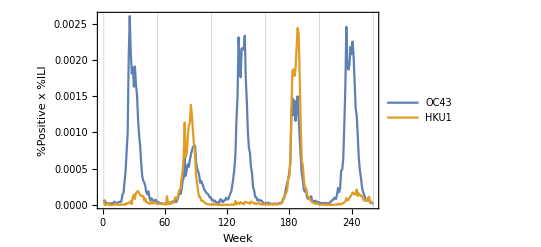

```mathematica
ListLinePlot[{{nrevssCDCweekind, nrevssCDCOC43}ᵀ,{nrevssCDCweekind, nrevssCDCHKU1}ᵀ}, PlotRange->All, Frame->{True,True,False,False}, FrameLabel->{"Week","%Positive x %ILI"}, BaseStyle->FontSize->14, ImageSize->400, PlotLegends->{"OC43","HKU1"}, GridLines->{Range[1, 1000, 52],{}}]
```

## Useful functions:

```mathematica
RangeN[from_, to_, nout_] := N[Range[from, to, (to-from)/(nout-1)]]
```

```mathematica
mult[vec_, factor_]:={#⟦1⟧, #⟦2⟧, factor*#⟦3⟧}&/@vec;
```

## Define forcing functions:

```mathematica
(*Seasonality function*)
betaval[t_, f_, maxR0_, phival_, gammaval_]:= gammaval*(f*maxR0/2*Cos[2*Pi*(t-phival)/52]+(maxR0 - f*maxR0/2))
```

## Define 2-strain model functions:

```mathematica
S1S2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
betaval[t,f,maxR0,phival,gammaval]*(I1S2[t]+I1E2[t]+I1I2[t]+I1R2[t])*S1S2[t]+p1[t]*S1S2[t]];
S1S2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
betaval[t,f,maxR0,phival,gammaval]*(S1I2[t]+E1I2[t]+I1I2[t]+R1I2[t])*S1S2[t]+p2[t]*S1S2[t]];
E1S2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*E1S2[t]];
E1S2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2[t]+E1I2[t]+I1I2[t]+R1I2[t])*E1S2[t]+(1-chi12val)*p2[t]*E1S2[t]];
S1E2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2[t]+I1E2[t]+I1I2[t]+I1R2[t])*S1E2[t]+(1-chi21val)*p1[t]*S1E2[t]];
S1E2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*S1E2[t]];
E1E2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*E1E2[t]];
E1E2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*E1E2[t]];
I1S2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*I1S2[t]];
I1S2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2[t]+E1I2[t]+I1I2[t]+R1I2[t])*I1S2[t]+(1-chi12val)*p2[t]*I1S2[t]];
S1I2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2[t]+I1E2[t]+I1I2[t]+I1R2[t])*S1I2[t]+(1-chi21val)*p1[t]*S1I2[t]];
S1I2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*S1I2[t]];
R1S2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma1val*R1S2[t]];
R1S2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2[t]+E1I2[t]+I1I2[t]+R1I2[t])*R1S2[t]+(1-chi12val)*p2[t]*R1S2[t]];
I1E2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*I1E2[t]];
I1E2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*I1E2[t]];
E1I2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*E1I2[t]];
E1I2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*E1I2[t]];
S1R2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2[t]+I1E2[t]+I1I2[t]+I1R2[t])*S1R2[t]+(1-chi21val)*p1[t]*S1R2[t]];
S1R2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma2val*S1R2[t]];
R1E2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma1val*R1E2[t]];
R1E2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*R1E2[t]];
I1I2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*I1I2[t]];
I1I2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*I1I2[t]];
E1R2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
nuval*E1R2[t]];
E1R2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma2val*E1R2[t]];
R1I2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma1val*R1I2[t]];
R1I2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*R1I2[t]];
I1R2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
gammaval*I1R2[t]];
I1R2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma2val*I1R2[t]];
R1R2c1[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma1val*R1R2[t]];
R1R2c2[t_,parms_]:=Module[{sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival},sigma1val=parms[[1]];
sigma2val=parms[[2]];
nuval=parms[[3]];
gammaval=parms[[4]];
chi12val=parms[[5]];
chi21val=parms[[6]];
f=parms[[7]];
maxR0=parms[[8]];
phival=parms[[9]];
sigma2val*R1R2[t]];
```

## Define 2-strain model solver:

```mathematica
runmodel2strain[parms_] := NDSolveValue[{
S1S2'[t]==-S1S2c1[t,parms]-S1S2c2[t,parms]+R1S2c1[t,parms]+S1R2c2[t,parms]-muval*S1S2[t]+muval,E1S2'[t]==-E1S2c1[t,parms]-E1S2c2[t,parms]+S1S2c1[t,parms]+E1R2c2[t,parms]-muval*E1S2[t],S1E2'[t]==-S1E2c1[t,parms]-S1E2c2[t,parms]+R1E2c1[t,parms]+S1S2c2[t,parms]-muval*S1E2[t],E1E2'[t]==-E1E2c1[t,parms]-E1E2c2[t,parms]+S1E2c1[t,parms]+E1S2c2[t,parms]-muval*E1E2[t],I1S2'[t]==-I1S2c1[t,parms]-I1S2c2[t,parms]+E1S2c1[t,parms]+I1R2c2[t,parms]-muval*I1S2[t],S1I2'[t]==-S1I2c1[t,parms]-S1I2c2[t,parms]+R1I2c1[t,parms]+S1E2c2[t,parms]-muval*S1I2[t],R1S2'[t]==-R1S2c1[t,parms]-R1S2c2[t,parms]+I1S2c1[t,parms]+R1R2c2[t,parms]-muval*R1S2[t],I1E2'[t]==-I1E2c1[t,parms]-I1E2c2[t,parms]+E1E2c1[t,parms]+I1S2c2[t,parms]-muval*I1E2[t],E1I2'[t]==-E1I2c1[t,parms]-E1I2c2[t,parms]+S1I2c1[t,parms]+E1E2c2[t,parms]-muval*E1I2[t],S1R2'[t]==-S1R2c1[t,parms]-S1R2c2[t,parms]+R1R2c1[t,parms]+S1I2c2[t,parms]-muval*S1R2[t],R1E2'[t]==-R1E2c1[t,parms]-R1E2c2[t,parms]+I1E2c1[t,parms]+R1S2c2[t,parms]-muval*R1E2[t],I1I2'[t]==-I1I2c1[t,parms]-I1I2c2[t,parms]+E1I2c1[t,parms]+I1E2c2[t,parms]-muval*I1I2[t],E1R2'[t]==-E1R2c1[t,parms]-E1R2c2[t,parms]+S1R2c1[t,parms]+E1I2c2[t,parms]-muval*E1R2[t],R1I2'[t]==-R1I2c1[t,parms]-R1I2c2[t,parms]+I1I2c1[t,parms]+R1E2c2[t,parms]-muval*R1I2[t],I1R2'[t]==-I1R2c1[t,parms]-I1R2c2[t,parms]+E1R2c1[t,parms]+I1I2c2[t,parms]-muval*I1R2[t],R1R2'[t]==-R1R2c1[t,parms]-R1R2c2[t,parms]+I1R2c1[t,parms]+R1I2c2[t,parms]-muval*R1R2[t],
p1'[t] == 0,
p2'[t] == 0 ,
WhenEvent[t ≥ importtime1, p1[t]-> kappaval],
WhenEvent[t > importtime1+importlength, p1[t]-> 0],
WhenEvent[t ≥ importtime2, p2[t]-> kappaval],
WhenEvent[t > importtime2+importlength, p2[t]-> 0],
S1S2[0]== 1,E1S2[0]==0 ,S1E2[0]==0,E1E2[0]==0,I1S2[0]==0,S1I2[0]==0,R1S2[0]==0,I1E2[0]==0,E1I2[0]==0,S1R2[0]==0,R1E2[0]==0,I1I2[0]==0,E1R2[0]==0,R1I2[0]==0,I1R2[0]==0,R1R2[0]==0, p1[0] == 0, p2[0] == 0
},
{S1S2,E1S2,S1E2,E1E2,I1S2,S1I2,R1S2,I1E2,E1I2,S1R2,R1E2,I1I2,E1R2,R1I2,I1R2,R1R2, p1, p2},
{t, 0, tmax}
]
```

## Define function to calculate log likelihood from the 2-strain parameters:

```mathematica
getll[sigma1val_?NumberQ, sigma2val_?NumberQ, nuval_?NumberQ, gammaval_?NumberQ, chi12val_?NumberQ, chi21val_?NumberQ, f_?NumberQ, maxR0_?NumberQ, phival_?NumberQ, sf_?NumberQ] := Module[
{parms, strain1sim1, strain2sim1,strain1sim2, strain2sim2, SSE1, SSE2, SSE, 
S1S2sol, E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol},

parms = {sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival};

{S1S2sol,E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol} = runmodel2strain[parms];

strain1sim1= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks1;
strain1sim2= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks2;
strain2sim1=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks1;
strain2sim2=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks2;

SSE1 = Total[(Select[Log[sf*strain1sim1]-Log[nrevssCDCOC43], NumberQ[#]&])^2] + Total[(Select[Log[sf*strain2sim1]-Log[nrevssCDCHKU1], NumberQ[#]&])^2];
SSE2 = Total[(Select[Log[sf*strain1sim2]-Log[nrevssCDCOC43], NumberQ[#]&])^2] + Total[(Select[Log[sf*strain2sim2]-Log[nrevssCDCHKU1], NumberQ[#]&])^2];

SSE = Min[SSE1, SSE2];

Return[-1/(2*(0.6^2))*SSE];

]
```

```mathematica
getsse[sigma1val_?NumberQ, sigma2val_?NumberQ, nuval_?NumberQ, gammaval_?NumberQ, chi12val_?NumberQ, chi21val_?NumberQ, f_?NumberQ, maxR0_?NumberQ, phival_?NumberQ, sf_?NumberQ] := Module[
{parms, strain1sim1, strain2sim1,strain1sim2, strain2sim2, SSE1, SSE2, SSE, 
S1S2sol, E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol},

parms = {sigma1val,sigma2val,nuval,gammaval,chi12val,chi21val,f,maxR0,phival};

{S1S2sol,E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol} = runmodel2strain[parms];

strain1sim1= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks1;
strain1sim2= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks2;
strain2sim1=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks1;
strain2sim2=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks2;

SSE1 = Total[(Select[Log[sf*strain1sim1]-Log[nrevssCDCOC43], NumberQ[#]&])^2] + Total[(Select[Log[sf*strain2sim1]-Log[nrevssCDCHKU1], NumberQ[#]&])^2];
SSE2 = Total[(Select[Log[sf*strain1sim2]-Log[nrevssCDCOC43], NumberQ[#]&])^2] + Total[(Select[Log[sf*strain2sim2]-Log[nrevssCDCHKU1], NumberQ[#]&])^2];

SSE = Min[SSE1, SSE2];

Return[SSE];

]
```

## Define 3-strain model functions:

```mathematica
S1S2S3c1[t]:=betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2S3[t]+p1[t]*S1S2S3[t]

S1S2S3c2[t]:=betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2S3[t]+p2[t]*S1S2S3[t]

S1S2S3c3[t]:=betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1S2S3[t]+p3[t]*S1S2S3[t]

S1S2E3c1[t]:=(1-chi31val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2E3[t]+(1-chi31val)*p1[t]*S1S2E3[t]

S1S2E3c2[t]:=(1-chi32val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2E3[t]+(1-chi32val)*p2[t]*S1S2E3[t]

S1S2E3c3[t]:=nuvalnCoV*S1S2E3[t]

S1S2I3c1[t]:=(1-chi31val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2I3[t]+(1-chi31val)*p1[t]*S1S2I3[t]

S1S2I3c2[t]:=(1-chi32val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2I3[t]+(1-chi32val)*p2[t]*S1S2I3[t]

S1S2I3c3[t]:=gammavalnCoV*S1S2I3[t]

S1S2R3c1[t]:=(1-chi31val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2R3[t]+(1-chi31val)*p1[t]*S1S2R3[t]

S1S2R3c2[t]:=(1-chi32val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2R3[t]+(1-chi32val)*p2[t]*S1S2R3[t]

S1S2R3c3[t]:=sigma3val*S1S2R3[t]

S1E2S3c1[t]:=(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2S3[t]+(1-chi21val)*p1[t]*S1E2S3[t]

S1E2S3c2[t]:=nuval*S1E2S3[t]

S1E2S3c3[t]:=(1-chi23val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1E2S3[t]+(1-chi23val)*p3[t]*S1E2S3[t]

S1E2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2E3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1E2E3[t]

S1E2E3c2[t]:=nuval*S1E2E3[t]

S1E2E3c3[t]:=nuvalnCoV*S1E2E3[t]

S1E2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2I3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1E2I3[t]

S1E2I3c2[t]:=nuval*S1E2I3[t]

S1E2I3c3[t]:=gammavalnCoV*S1E2I3[t]

S1E2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2R3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1E2R3[t]

S1E2R3c2[t]:=nuval*S1E2R3[t]

S1E2R3c3[t]:=sigma3val*S1E2R3[t]

S1I2S3c1[t]:=(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2S3[t]+(1-chi21val)*p1[t]*S1I2S3[t]

S1I2S3c2[t]:=gammaval*S1I2S3[t]

S1I2S3c3[t]:=(1-chi23val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1I2S3[t]+(1-chi23val)*p3[t]*S1I2S3[t]

S1I2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2E3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1I2E3[t]

S1I2E3c2[t]:=gammaval*S1I2E3[t]

S1I2E3c3[t]:=nuvalnCoV*S1I2E3[t]

S1I2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2I3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1I2I3[t]

S1I2I3c2[t]:=gammaval*S1I2I3[t]

S1I2I3c3[t]:=gammavalnCoV*S1I2I3[t]

S1I2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2R3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1I2R3[t]

S1I2R3c2[t]:=gammaval*S1I2R3[t]

S1I2R3c3[t]:=sigma3val*S1I2R3[t]

S1R2S3c1[t]:=(1-chi21val)*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2S3[t]+(1-chi21val)*p1[t]*S1R2S3[t]

S1R2S3c2[t]:=sigma2val*S1R2S3[t]

S1R2S3c3[t]:=(1-chi23val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1R2S3[t]+(1-chi23val)*p3[t]*S1R2S3[t]

S1R2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2E3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1R2E3[t]

S1R2E3c2[t]:=sigma2val*S1R2E3[t]

S1R2E3c3[t]:=nuvalnCoV*S1R2E3[t]

S1R2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2I3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1R2I3[t]

S1R2I3c2[t]:=sigma2val*S1R2I3[t]

S1R2I3c3[t]:=gammavalnCoV*S1R2I3[t]

S1R2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,f,maxR0,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2R3[t]+(1-Max[chi21val,chi31val])*p1[t]*S1R2R3[t]

S1R2R3c2[t]:=sigma2val*S1R2R3[t]

S1R2R3c3[t]:=sigma3val*S1R2R3[t]

E1S2S3c1[t]:=nuval*E1S2S3[t]

E1S2S3c2[t]:=(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2S3[t]+(1-chi12val)*p2[t]*E1S2S3[t]

E1S2S3c3[t]:=(1-chi13val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1S2S3[t]+(1-chi13val)*p3[t]*E1S2S3[t]

E1S2E3c1[t]:=nuval*E1S2E3[t]

E1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t]*E1S2E3[t]

E1S2E3c3[t]:=nuvalnCoV*E1S2E3[t]

E1S2I3c1[t]:=nuval*E1S2I3[t]

E1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t]*E1S2I3[t]

E1S2I3c3[t]:=gammavalnCoV*E1S2I3[t]

E1S2R3c1[t]:=nuval*E1S2R3[t]

E1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t]*E1S2R3[t]

E1S2R3c3[t]:=sigma3val*E1S2R3[t]

E1E2S3c1[t]:=nuval*E1E2S3[t]

E1E2S3c2[t]:=nuval*E1E2S3[t]

E1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*E1E2S3[t]

E1E2E3c1[t]:=nuval*E1E2E3[t]

E1E2E3c2[t]:=nuval*E1E2E3[t]

E1E2E3c3[t]:=nuvalnCoV*E1E2E3[t]

E1E2I3c1[t]:=nuval*E1E2I3[t]

E1E2I3c2[t]:=nuval*E1E2I3[t]

E1E2I3c3[t]:=gammavalnCoV*E1E2I3[t]

E1E2R3c1[t]:=nuval*E1E2R3[t]

E1E2R3c2[t]:=nuval*E1E2R3[t]

E1E2R3c3[t]:=sigma3val*E1E2R3[t]

E1I2S3c1[t]:=nuval*E1I2S3[t]

E1I2S3c2[t]:=gammaval*E1I2S3[t]

E1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*E1I2S3[t]

E1I2E3c1[t]:=nuval*E1I2E3[t]

E1I2E3c2[t]:=gammaval*E1I2E3[t]

E1I2E3c3[t]:=nuvalnCoV*E1I2E3[t]

E1I2I3c1[t]:=nuval*E1I2I3[t]

E1I2I3c2[t]:=gammaval*E1I2I3[t]

E1I2I3c3[t]:=gammavalnCoV*E1I2I3[t]

E1I2R3c1[t]:=nuval*E1I2R3[t]

E1I2R3c2[t]:=gammaval*E1I2R3[t]

E1I2R3c3[t]:=sigma3val*E1I2R3[t]

E1R2S3c1[t]:=nuval*E1R2S3[t]

E1R2S3c2[t]:=sigma2val*E1R2S3[t]

E1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*E1R2S3[t]

E1R2E3c1[t]:=nuval*E1R2E3[t]

E1R2E3c2[t]:=sigma2val*E1R2E3[t]

E1R2E3c3[t]:=nuvalnCoV*E1R2E3[t]

E1R2I3c1[t]:=nuval*E1R2I3[t]

E1R2I3c2[t]:=sigma2val*E1R2I3[t]

E1R2I3c3[t]:=gammavalnCoV*E1R2I3[t]

E1R2R3c1[t]:=nuval*E1R2R3[t]

E1R2R3c2[t]:=sigma2val*E1R2R3[t]

E1R2R3c3[t]:=sigma3val*E1R2R3[t]

I1S2S3c1[t]:=gammaval*I1S2S3[t]

I1S2S3c2[t]:=(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2S3[t]+(1-chi12val)*p2[t]*I1S2S3[t]

I1S2S3c3[t]:=(1-chi13val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1S2S3[t]+(1-chi13val)*p3[t]*I1S2S3[t]

I1S2E3c1[t]:=gammaval*I1S2E3[t]

I1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t]*I1S2E3[t]

I1S2E3c3[t]:=nuvalnCoV*I1S2E3[t]

I1S2I3c1[t]:=gammaval*I1S2I3[t]

I1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t]*I1S2I3[t]

I1S2I3c3[t]:=gammavalnCoV*I1S2I3[t]

I1S2R3c1[t]:=gammaval*I1S2R3[t]

I1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t]*I1S2R3[t]

I1S2R3c3[t]:=sigma3val*I1S2R3[t]

I1E2S3c1[t]:=gammaval*I1E2S3[t]

I1E2S3c2[t]:=nuval*I1E2S3[t]

I1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*I1E2S3[t]

I1E2E3c1[t]:=gammaval*I1E2E3[t]

I1E2E3c2[t]:=nuval*I1E2E3[t]

I1E2E3c3[t]:=nuvalnCoV*I1E2E3[t]

I1E2I3c1[t]:=gammaval*I1E2I3[t]

I1E2I3c2[t]:=nuval*I1E2I3[t]

I1E2I3c3[t]:=gammavalnCoV*I1E2I3[t]

I1E2R3c1[t]:=gammaval*I1E2R3[t]

I1E2R3c2[t]:=nuval*I1E2R3[t]

I1E2R3c3[t]:=sigma3val*I1E2R3[t]

I1I2S3c1[t]:=gammaval*I1I2S3[t]

I1I2S3c2[t]:=gammaval*I1I2S3[t]

I1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*I1I2S3[t]

I1I2E3c1[t]:=gammaval*I1I2E3[t]

I1I2E3c2[t]:=gammaval*I1I2E3[t]

I1I2E3c3[t]:=nuvalnCoV*I1I2E3[t]

I1I2I3c1[t]:=gammaval*I1I2I3[t]

I1I2I3c2[t]:=gammaval*I1I2I3[t]

I1I2I3c3[t]:=gammavalnCoV*I1I2I3[t]

I1I2R3c1[t]:=gammaval*I1I2R3[t]

I1I2R3c2[t]:=gammaval*I1I2R3[t]

I1I2R3c3[t]:=sigma3val*I1I2R3[t]

I1R2S3c1[t]:=gammaval*I1R2S3[t]

I1R2S3c2[t]:=sigma2val*I1R2S3[t]

I1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*I1R2S3[t]

I1R2E3c1[t]:=gammaval*I1R2E3[t]

I1R2E3c2[t]:=sigma2val*I1R2E3[t]

I1R2E3c3[t]:=nuvalnCoV*I1R2E3[t]

I1R2I3c1[t]:=gammaval*I1R2I3[t]

I1R2I3c2[t]:=sigma2val*I1R2I3[t]

I1R2I3c3[t]:=gammavalnCoV*I1R2I3[t]

I1R2R3c1[t]:=gammaval*I1R2R3[t]

I1R2R3c2[t]:=sigma2val*I1R2R3[t]

I1R2R3c3[t]:=sigma3val*I1R2R3[t]

R1S2S3c1[t]:=sigma1val*R1S2S3[t]

R1S2S3c2[t]:=(1-chi12val)*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2S3[t]+(1-chi12val)*p2[t]*R1S2S3[t]

R1S2S3c3[t]:=(1-chi13val)*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1S2S3[t]+(1-chi13val)*p3[t]*R1S2S3[t]

R1S2E3c1[t]:=sigma1val*R1S2E3[t]

R1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t]*R1S2E3[t]

R1S2E3c3[t]:=nuvalnCoV*R1S2E3[t]

R1S2I3c1[t]:=sigma1val*R1S2I3[t]

R1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t]*R1S2I3[t]

R1S2I3c3[t]:=gammavalnCoV*R1S2I3[t]

R1S2R3c1[t]:=sigma1val*R1S2R3[t]

R1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,f,maxR0,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t]*R1S2R3[t]

R1S2R3c3[t]:=sigma3val*R1S2R3[t]

R1E2S3c1[t]:=sigma1val*R1E2S3[t]

R1E2S3c2[t]:=nuval*R1E2S3[t]

R1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*R1E2S3[t]

R1E2E3c1[t]:=sigma1val*R1E2E3[t]

R1E2E3c2[t]:=nuval*R1E2E3[t]

R1E2E3c3[t]:=nuvalnCoV*R1E2E3[t]

R1E2I3c1[t]:=sigma1val*R1E2I3[t]

R1E2I3c2[t]:=nuval*R1E2I3[t]

R1E2I3c3[t]:=gammavalnCoV*R1E2I3[t]

R1E2R3c1[t]:=sigma1val*R1E2R3[t]

R1E2R3c2[t]:=nuval*R1E2R3[t]

R1E2R3c3[t]:=sigma3val*R1E2R3[t]

R1I2S3c1[t]:=sigma1val*R1I2S3[t]

R1I2S3c2[t]:=gammaval*R1I2S3[t]

R1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*R1I2S3[t]

R1I2E3c1[t]:=sigma1val*R1I2E3[t]

R1I2E3c2[t]:=gammaval*R1I2E3[t]

R1I2E3c3[t]:=nuvalnCoV*R1I2E3[t]

R1I2I3c1[t]:=sigma1val*R1I2I3[t]

R1I2I3c2[t]:=gammaval*R1I2I3[t]

R1I2I3c3[t]:=gammavalnCoV*R1I2I3[t]

R1I2R3c1[t]:=sigma1val*R1I2R3[t]

R1I2R3c2[t]:=gammaval*R1I2R3[t]

R1I2R3c3[t]:=sigma3val*R1I2R3[t]

R1R2S3c1[t]:=sigma1val*R1R2S3[t]

R1R2S3c2[t]:=sigma2val*R1R2S3[t]

R1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,fnCoV,maxR0nCoV,phival,gammavalnCoV]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t]*R1R2S3[t]

R1R2E3c1[t]:=sigma1val*R1R2E3[t]

R1R2E3c2[t]:=sigma2val*R1R2E3[t]

R1R2E3c3[t]:=nuvalnCoV*R1R2E3[t]

R1R2I3c1[t]:=sigma1val*R1R2I3[t]

R1R2I3c2[t]:=sigma2val*R1R2I3[t]

R1R2I3c3[t]:=gammavalnCoV*R1R2I3[t]

R1R2R3c1[t]:=sigma1val*R1R2R3[t]

R1R2R3c2[t]:=sigma2val*R1R2R3[t]

R1R2R3c3[t]:=sigma3val*R1R2R3[t]
```

## Define 3-strain model solver:

```mathematica
runmodel3strain[] := NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
cuminfnCoV'[t]== S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
p1'[t] == 0,
p2'[t] == 0 ,
p3'[t] == 0 ,
WhenEvent[t ≥ importtime1, p1[t]-> kappaval],
WhenEvent[t > importtime1+importlength, p1[t]-> 0],
WhenEvent[t ≥ importtime2, p2[t]-> kappaval],
WhenEvent[t > importtime2+importlength, p2[t]-> 0],
WhenEvent[t ≥ importtime3, p3[t]-> kappaval],
WhenEvent[t > importtime3+importlength, p3[t]-> 0],
(*WhenEvent[cuminf[t] > 1, "StopIntegration"],*)
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0,cuminfnCoV[0]==0,  p1[0] == 0, p2[0] == 0, p3[0] == 0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf, cuminfnCoV, p1, p2, p3},
{t, 0, tmax}
];
```

## Set default parameter values:

Set 0 (the best and right ones it seems):

```mathematica
rundefaults[]:=(sigma1val = 1/44.94837857251785; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma2val = 1/44.96099593027429; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma3val = 1/104; (*Waning immunity rate, strain 1, weeks; default 1/40*)
nuval = 1/(2.999751226892689/7);  (*Rate of progression to infection, weeks; default 1/1*)
nuvalnCoV = 1/(4.6/7);
gammaval = 1/(5.043512653991342/7); (*Rate of recovery, weeks; default 1/1*)
gammavalnCoV = 1/(5/7);
chi12val = 0.7789022405467717; (*Cross immunity, strain 1 to 2*)
chi21val =0.5068431811943369; (*Cross immunity, strain 2 to 1*)
chi13val=0.0; (*Cross immunity, strain 1 to 2*)
chi31val=0.7; (*Cross immunity, strain 3 to 1*)
chi23val=0.0; (*Cross immunity, strain 2 to 3*)
chi32val=0.7; (*Cross immunity, strain 3 to 2*)
f = 0.21519566939603102;
fnCoV = 0.21519566939603102;
maxR0 =(*2.6*)2.1986663426600286 ;
maxR0nCoV =2.1986663426600286;
phival=2.036402516800722; (*Phase shift for seasonal R0 (weeks)*)
kappaval = 0.01; (*Boost from importations*)
importtime1 = 52; (*Importation time for strain 1, weeks*)
importtime2 = 0.0001;  (*Importation time for strain 2, weeks*)
importtime3= 52*100(*52*24+12*);  (*Importation time for strain 3, weeks*)
importlength = 0.5; (*How long does an importation boost transmission, in weeks?*)
muval = 1/(80*52); (* birth rate, in weeks *) 
scalingfactor =0.05993353450606306; (*Conversion between prevalence and (% positive * % ILI) *)
);
rundefaults[];
```

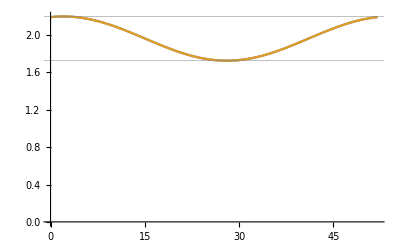

```mathematica
Plot[{betaval[t,fnCoV, maxR0nCoV, phival, 1],betaval[t,f, maxR0, phival, 1],},{t, 0, 52}, PlotRange->{0, maxR0nCoV}, GridLines->{{},{maxR0nCoV, maxR0nCoV - fnCoV*maxR0nCoV, maxR0, maxR0 - f*maxR0}}]
```

```mathematica
tmax = 52*30; (*Simulation timespan, weeks*)
```

```mathematica
extractweeks1 = Range[52*24.5, 52*29.5, 1];
extractweeks2 = Range[52*23.5, 52*28.5, 1];
```

```mathematica
plotwindow = {52*21.5, 52*28.5}(*{52*20.5, 52*27.5}*); (*Time span for plotting*)
plotrangemax = 0.6; (*Max plotting value *)
importbarchar = {Black, Thick}; (*For plotting the bar marking the importation time*)
yearbarchar = {Gray, Thin}; (*For marking years*)
fs = 18; (*Plot font size*)
imsz = 475; (*plot image size*)
ncovticks = {100*scalingfactor*#, ToString[N[1000*#]]}&/@N[FindDivisions[{0, 1/(100*scalingfactor)*plotrangemax},5]];
oc43char = {Blue,Thickness[0.008], Opacity[0.5]}; (*Plotting characteristics for HCoV-OC43*)
hku1char = {Red, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-HKU1*)
ncovchar={Black, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-SARS-CoV-2*)
totalchar={Black, Thickness[0.004], Opacity[0.5],Dashed};(*Plotting characteristics for the total prevalence curve*)
pandemicintro = 52*23 + (31 + 29 + 11)/7(*52*22 + (31 + 29 + 11)/7*);
```

## Do a maximization:

```mathematica
(*Clear[f];
Clear[ϕ];
Clear[maxR0];*)
```

```mathematica
(*fit1 = Timing[NMaximize[{
getll[N[1/σ1inv],N[1/σ2inv], N[7/νd], N[7/γd], N[χ12], N[χ21],N[f], N[maxR0],N[ϕ],N[sf]],
35<σ1inv<45, 
35 <σ2inv<45,
2 <νd< 10,
2 < γd < 10,
0.1 < χ12 < 0.9,
0.1 < χ21 < 0.9,
0<f<0.5,
1.2 <maxR0 < 3,
-8 < ϕ < 8, 
0.01 < sf < 0.1 }
,{σ1inv, σ2inv,νd, γd, χ12,χ21,f,maxR0, ϕ, sf}, Method->"NelderMead", AccuracyGoal->Infinity, PrecisionGoal->4, MaxIterations->1000]]*)
```

## Plot one fit to verify and plot residuals:

```mathematica
{S1S2sol,E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol} = runmodel2strain[{1/44.94837857251785, 1/44.96099593027429, 7/2.999751226892689, 7/5.043512653991342, 0.7789022405467717, 0.5068431811943369, 0.21519566939603102, 2.1986663426600286, 2.036402516800722}];
```

```mathematica
{S1S2sol,E1S2sol,S1E2sol,E1E2sol,I1S2sol,S1I2sol,R1S2sol,I1E2sol,E1I2sol,S1R2sol,R1E2sol,I1I2sol,E1R2sol,R1I2sol,I1R2sol,R1R2sol, p1sol, p2sol} = runmodel2strain[{sigma1val, sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phival}];
```

```mathematica
strain1sim1= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks1;
strain1sim2= (I1S2sol[#] + I1E2sol[#] + I1I2sol[#] + I1R2sol[#])&/@extractweeks2;
strain2sim1=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks1;
strain2sim2=(S1I2sol[#] + E1I2sol[#] + I1I2sol[#] + R1I2sol[#])&/@extractweeks2;
```

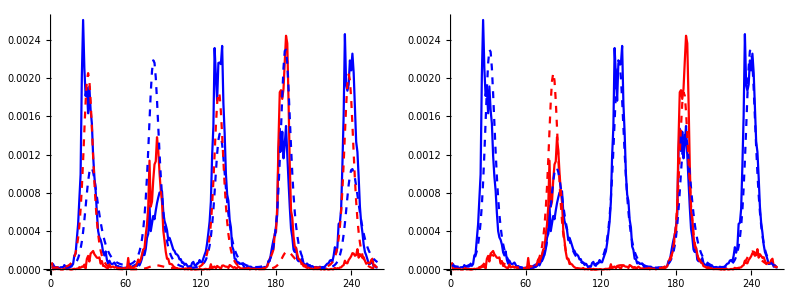

```mathematica
Grid[{{
ListLinePlot[{{nrevssCDCweekind, nrevssCDCOC43}ᵀ,{nrevssCDCweekind, nrevssCDCHKU1}ᵀ,{nrevssCDCweekind,  0.06481959900976779*strain1sim1}ᵀ,{nrevssCDCweekind,  0.06481959900976779*strain2sim1}ᵀ}, PlotRange->All, PlotStyle->{{Blue}, {Red}, {Blue,Dashed}, {Red,Dashed}},ImageSize->300],
ListLinePlot[{{nrevssCDCweekind, nrevssCDCOC43}ᵀ,{nrevssCDCweekind, nrevssCDCHKU1}ᵀ,{nrevssCDCweekind,  0.06481959900976779*strain1sim2}ᵀ,{nrevssCDCweekind,  0.06481959900976779*strain2sim2}ᵀ}, PlotRange->All, PlotStyle->{{Blue}, {Red}, {Blue,Dashed}, {Red,Dashed}},ImageSize->300]
}}]
```

```mathematica
rundefaults[];
sol = runmodel3strain[];
```

```mathematica
oc43 = Flatten[Table[Evaluate[scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])/.sol],{t, extractweeks2}]];
hku1 = Flatten[Table[Evaluate[scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])/.sol],{t, extractweeks2}]];
```

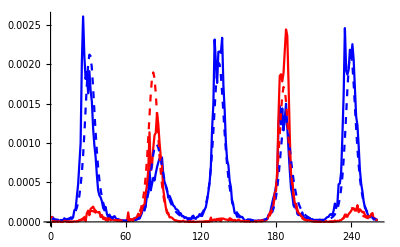

```mathematica
ListLinePlot[{{nrevssCDCweekind, nrevssCDCOC43}ᵀ,{nrevssCDCweekind, nrevssCDCHKU1}ᵀ,{nrevssCDCweekind,oc43}ᵀ,{nrevssCDCweekind, hku1}ᵀ}, PlotRange->All, PlotStyle->{{Blue}, {Red}, {Blue,Dashed}, {Red,Dashed}}]
```

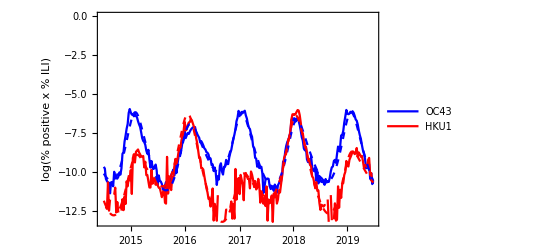

```mathematica
figlogfits = ListLinePlot[{{nrevssCDCweekind, Log[nrevssCDCOC43]}ᵀ,{nrevssCDCweekind, Log[nrevssCDCHKU1]}ᵀ,{nrevssCDCweekind, Log[oc43]}ᵀ,{nrevssCDCweekind, Log[hku1]}ᵀ}, PlotRange->All, PlotStyle->{{Blue}, {Red}, {Blue,Dashed}, {Red,Dashed}}, Frame->{True, True, False, False}, FrameTicks->{{{27, "2015"}, {79,"2016"}, {132,"2017"}, {184,"2018"}, {236,"2019"}}, Automatic}, BaseStyle->FontSize->14, ImageSize->400, FrameLabel->{None,"log(% positive x % ILI)"}, PlotLegends->{"OC43", "HKU1"}]
```

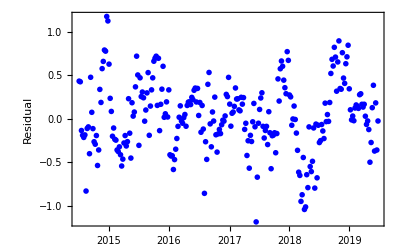

```mathematica
figoc43residuals = ListPlot[{nrevssCDCweekind, Log[nrevssCDCOC43] - Log[oc43]}ᵀ, Frame->{True,True,False,False}, FrameTicks->{{{27, "2015"}, {79, "2016"}, {132, "2017"}, {184,"2018"}, {236,"2019"}}, Automatic}, BaseStyle->FontSize->14, ImageSize->400, PlotStyle->{Blue,PointSize->.01}, FrameLabel->{None,"Residual"}, PlotRange->All]
```

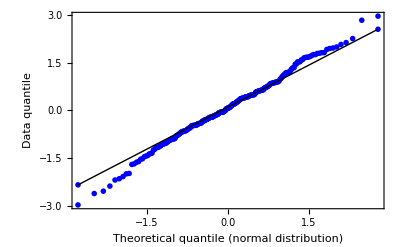

```mathematica
figoc43qq = QuantilePlot[(Log[1*nrevssCDCOC43] - Log[oc43])/StandardDeviation[Log[1*nrevssCDCOC43] - Log[oc43]], NormalDistribution[0,1], PlotRange->All, PlotStyle->{Blue, PointSize->0.01}, Frame->True, FrameLabel->{"Theoretical quantile (normal distribution)","Data quantile"}, BaseStyle->FontSize->14,  ImageSize->400]
```

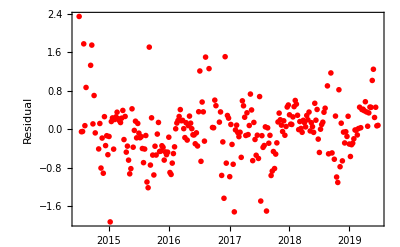

```mathematica
fighku1residuals = ListPlot[{nrevssCDCweekind, (Log[nrevssCDCHKU1] - Log[hku1])}ᵀ, Frame->{True,True,False,False}, FrameTicks->{{{27, "2015"}, {79, "2016"}, {132, "2017"}, {184,"2018"}, {236,"2019"}}, Automatic}, BaseStyle->FontSize->14, ImageSize->400, PlotStyle->{Red,PointSize->.01}, FrameLabel->{None,"Residual"}, PlotRange->All]
```

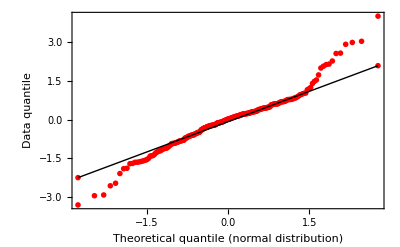

```mathematica
fighku1qq = QuantilePlot[Select[Log[nrevssCDCHKU1] - Log[hku1],NumberQ[#]&] / StandardDeviation[Select[Log[nrevssCDCHKU1] - Log[hku1],NumberQ[#]&]], NormalDistribution[0,1], PlotRange->All, PlotStyle->{Red, PointSize->0.01}, Frame->True, FrameLabel->{"Theoretical quantile (normal distribution)","Data quantile"}, BaseStyle->FontSize->14,  ImageSize->400]
```

```mathematica
(*Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/logfits.pdf", figlogfits];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/oc43residuals.pdf", figoc43residuals];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/oc43qq.pdf", figoc43qq];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/hku1residuals.pdf",fighku1residuals];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/hku1qq.pdf",fighku1qq];

Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/logfits.png",figlogfits];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/oc43residuals.png",figoc43residuals];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/oc43qq.png",figoc43qq];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/hku1residuals.png",fighku1residuals];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/hku1qq.png",fighku1qq];*)
```

## Plot some slice likelihoods:

```mathematica
getll[sigma1val, sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor]
```

-174.323

```mathematica
sigma1invrange = Table[1/sigma1val+delta,{delta, -10, 20, 0.2}];
sigma1proftemp = Table[getsse[1/(sigma1inv), sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor],{sigma1inv,sigma1invrange}];
```

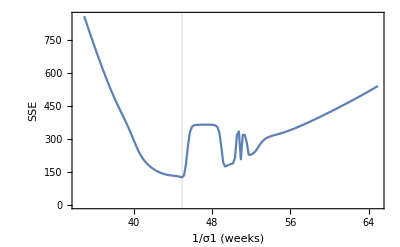

```mathematica
figsigma1prof = ListLinePlot[{sigma1invrange,sigma1proftemp}ᵀ, 
Frame->True, GridLines->{{{1/sigma1val, {Black, Opacity[1]}}},{}},
FrameLabel->{"1/σ1 (weeks)", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
sigma2invrange = Table[1/sigma2val+delta,{delta, -10, 20, 0.2}];
sigma2proftemp = Table[getsse[sigma1val, 1/(sigma2inv), nuval, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor],{sigma2inv,sigma2invrange}];
```

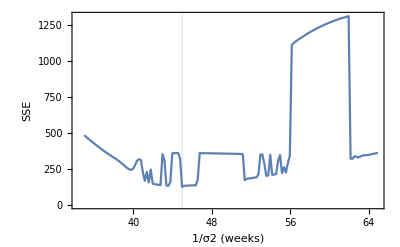

```mathematica
figsigma2prof = ListLinePlot[{sigma2invrange,sigma2proftemp}ᵀ, 
Frame->True, GridLines->{{{1/sigma2val, {Black, Opacity[1]}}},{}},
FrameLabel->{"1/σ2 (weeks)", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
nudrange = Table[7/nuval+delta,{delta, -1, 2, 0.05}];
nuproftemp = Table[getsse[sigma1val, sigma2val, 7/nud, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor],{nud,nudrange}];
```

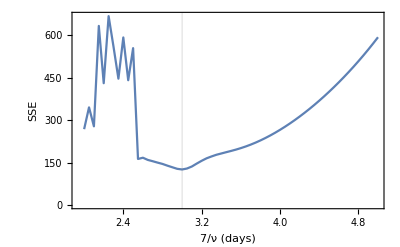

```mathematica
fignuprof = ListLinePlot[{nudrange,nuproftemp}ᵀ, 
Frame->True, GridLines->{{{7/nuval, {Black, Opacity[1]}}},{}},
FrameLabel->{"7/ν (days)", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
gammadrange = Table[7/gammaval+delta,{delta, -2, 2, 0.05}];
gammaproftemp = Table[getsse[sigma1val, sigma2val, nuval, 7/gammad, chi12val, chi21val, f, maxR0, phival, scalingfactor],{gammad,gammadrange}];
```

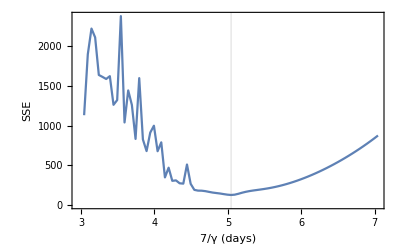

```mathematica
figgammaprof = ListLinePlot[{gammadrange,gammaproftemp}ᵀ, 
Frame->True, GridLines->{{{7/gammaval, {Black, Opacity[1]}}},{}},
FrameLabel->{"7/γ (days)", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
chi12range = Table[chi12val+delta,{delta, -0.2, 0.2, 0.01}];
chi12proftemp = Table[getsse[sigma1val, sigma2val, nuval, gammaval, chi12, chi21val, f, maxR0, phival, scalingfactor],{chi12,chi12range}];
```

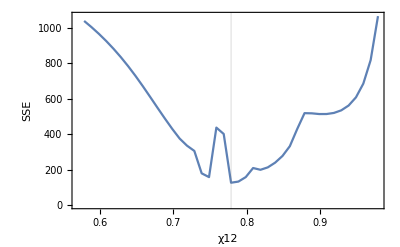

```mathematica
figchi12prof = ListLinePlot[{chi12range,chi12proftemp}ᵀ, 
Frame->True, GridLines->{{{chi12val, {Black, Opacity[1]}}},{}},
FrameLabel->{"χ12", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
chi21range = Table[chi21val+delta,{delta, -0.2, 0.2, 0.01}];
chi21proftemp = Table[getsse[sigma1val, sigma2val, nuval, gammaval, chi12val, chi21, f, maxR0, phival, scalingfactor],{chi21,chi21range}];
```

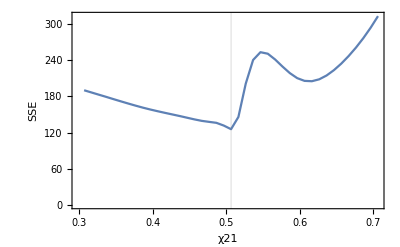

```mathematica
figchi21prof = ListLinePlot[{chi21range,chi21proftemp}ᵀ, 
Frame->True, GridLines->{{{chi21val, {Black, Opacity[1]}}},{}},
FrameLabel->{"χ21", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
frange = Table[f+delta,{delta, -0.1, 0.2, 0.01}];
fproftemp = Table[getsse[sigma1val, sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor],{f,frange}];
```

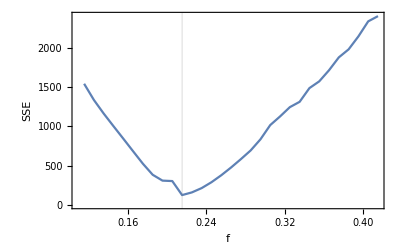

```mathematica
figfprof = ListLinePlot[{frange,fproftemp}ᵀ, 
Frame->True, GridLines->{{{f, {Black, Opacity[1]}}},{}},
FrameLabel->{"f", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
maxR0range = Table[maxR0+delta,{delta, -1, 1.5, 0.2}];
maxR0proftemp = Table[getsse[sigma1val, sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phival, scalingfactor],{maxR0,maxR0range}];
```

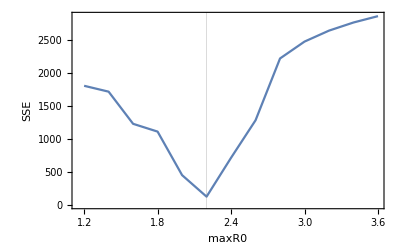

```mathematica
figmaxR0prof = ListLinePlot[{maxR0range,maxR0proftemp}ᵀ, 
Frame->True, GridLines->{{{maxR0, {Black, Opacity[1]}}},{}},
FrameLabel->{"maxR0", "SSE"}, BaseStyle->FontSize->14, ImageSize->400]
```

```mathematica
phirange = Table[phival+delta,{delta, -8, 8, 0.2}];
phiproftemp = Table[getsse[sigma1val, sigma2val, nuval, gammaval, chi12val, chi21val, f, maxR0, phi, scalingfactor],{phi,phirange}];
```

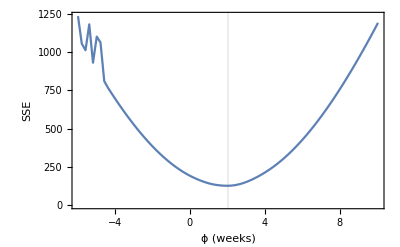

```mathematica
figphiprof = ListLinePlot[{phirange,phiproftemp}ᵀ, 
Frame->True, GridLines->{{{phival, {Black, Opacity[1]}}},{}},
FrameLabel->{"ϕ (weeks)", "SSE"}, BaseStyle->FontSize->14, ImageSize->400, Axes->None]
```

```mathematica
(*Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilesigma1.pdf", figsigma1prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilesigma2.pdf", figsigma2prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilenu.pdf",fignuprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilegamma.pdf",figgammaprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilechi12.pdf",figchi12prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilechi21.pdf",figchi21prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilef.pdf",figfprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilemaxR0.pdf",figmaxR0prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilephi.pdf",figphiprof];

Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilesigma1.png", figsigma1prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilesigma2.png", figsigma2prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilenu.png",fignuprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilegamma.png",figgammaprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilechi12.png",figchi12prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilechi21.png",figchi21prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilef.png",figfprof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilemaxR0.png",figmaxR0prof];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/profilephi.png",figphiprof];
*)
```

## Run some scenarios (Figure 3):

### 3A: Annual outbreaks after Week 12 introduction 30/0 | 40 | wpandemic:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.3;
chi32val = 0.3;
chi13val = 0;
chi23val = 0;
sigma3val = 1/40;
importtime3 = pandemicintro;
fnCoV = (*0.32*)0.21474422183819522;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

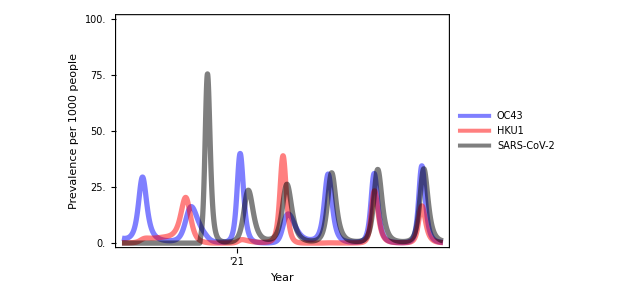

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3AhighR.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3AhighR.png",figinvasion];
```

### 3B: Sporadic outbreaks if longer-term immunity: 70/0 | 104 | w8:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = pandemicintro;
fnCoV = 0.21474422183819522;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

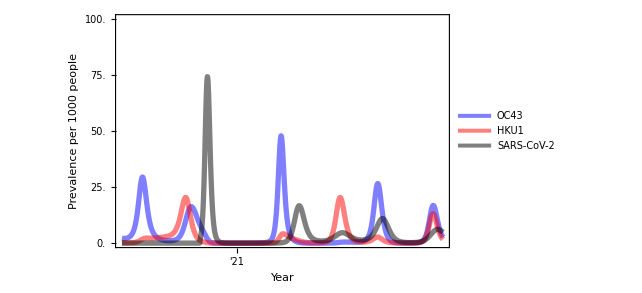

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3BhighR.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3BhighR.png",figinvasion];
```

### 3C: More seasonality will help flatten the curve: 70/0 | 104 | wpandemic | f 0.4:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = pandemicintro;
fnCoV = 0.4;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

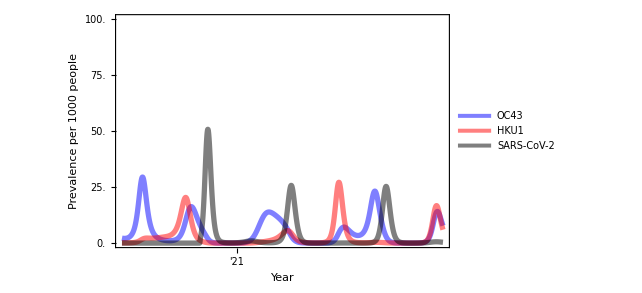

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3ChighR.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3ChighR.png",figinvasion];
```

### 3D: Permanent immunity leads to die-out: 70/0 | ∞ | wpandemic:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/Infinity;
importtime3 = pandemicintro;
fnCoV = (*0.32*)0.21474422183819522;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

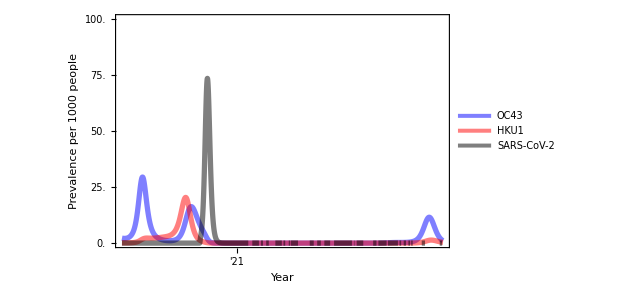

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3DhighR.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3DhighR.png",figinvasion];
```

### 3E: Cross-immunity could lead to a re-surgence late: 30/30 | 104 | w32 | f 0.4:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.3;
chi32val = 0.3;
chi13val = 0.3;
chi23val = 0.3;
sigma3val = 1/104;
importtime3 = pandemicintro(*52*23+ 32*);
fnCoV = 0.4(*0.32*)(*0.21474422183819522*);
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

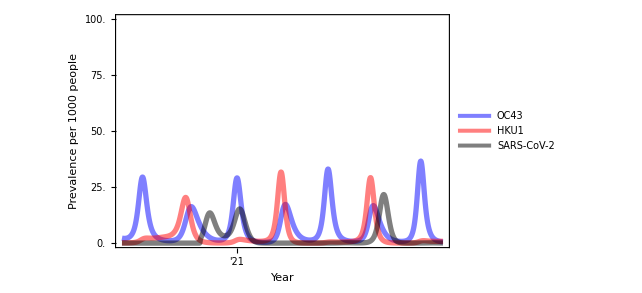

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3EhighR.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3EhighR.png",figinvasion];
```

## Sort out the table:

```mathematica
rundefaults[];
```

```mathematica
χ3Xvals={{0.7, 0},{0.7, 0.3},{0.3,0},{0,0}};
σ3vals = {{1/40}, {1/104}, {0}};
importtime3vals = {{52*23+4},{52*23+16},{52*23+28},{52*23+40}}; 
fvals = {{0.1}, {0.2}, {0.4}};
```

```mathematica
paramsets = Partition[Flatten[Table[Join[χ3X, σ3, importtime3, f], {χ3X, χ3Xvals}, {σ3, σ3vals}, {importtime3, importtime3vals},{f, fvals}]],5];
```

```mathematica
cuminfvec = {};
cuminfnCoVvec = {};
peakinfectedvec = {};
peakinfectednCoVvec = {};
```

```mathematica
Do[
chi31val = params⟦1⟧;
chi32val = params⟦1⟧;
chi13val = params⟦2⟧;
chi23val = params⟦2⟧;
sigma3val = params⟦3⟧;
importtime3 = params⟦4⟧;
fnCoV = params⟦5⟧;

sol = runmodel3strain[];

cuminftags = Flatten[Table[Evaluate[scalingfactor*cuminf[t]
/.sol],{t,plotwindow⟦1⟧,plotwindow⟦2⟧, 52}]];
cuminfnCoVtags = Flatten[Table[Evaluate[cuminfnCoV[t]
/.sol],{t,plotwindow⟦1⟧,plotwindow⟦2⟧, 52}]];

cuminfbyseason = Drop[cuminftags,1] - Drop[cuminftags,-1];
cuminfnCoVbyseason = Drop[cuminfnCoVtags,1] - Drop[cuminfnCoVtags,-1];

cuminfvec = Join[cuminfvec, {cuminfbyseason}];
cuminfnCoVvec = Join[cuminfnCoVvec, {cuminfnCoVbyseason}];

dailyinfected = Flatten[Table[Evaluate[scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]];

dailyinfectednCoV = Flatten[Table[Evaluate[(S1S2I3[t] + S1E2I3[t] + S1I2I3[t] + S1R2I3[t] + E1S2I3[t] + E1E2I3[t] + E1I2I3[t] + E1R2I3[t] + I1S2I3[t] + I1E2I3[t] + I1I2I3[t] + I1R2I3[t] + R1S2I3[t] + R1E2I3[t] + R1I2I3[t] + R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]];

peakinfected = Max[#]&/@Partition[dailyinfected,Length[dailyinfected]/7];
peakinfectedvec = Join[peakinfectedvec,{ peakinfected}];

peakinfectednCoV = Max[#]&/@Partition[dailyinfectednCoV,Length[dailyinfectednCoV]/7];
peakinfectednCoVvec = Join[peakinfectednCoVvec,{ peakinfectednCoV}];

(*Print[params];*)

,{params, paramsets}]
```

NDSolve::ndsz: At t == 1416.07, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1430.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1482.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1430.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3","f", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*cuminfvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3","f", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 1000*cuminfnCoVvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3", "f", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*peakinfectedvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3","f",  "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 1000*peakinfectednCoVvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

### Check the rows:

#### Define parameter values:

```mathematica
rundefaults[];
chi31val=0.7;
chi32val = 0.7;
chi13val = 0.0;
chi23val = 0.0;
sigma3val = 1/40;
importtime3 = (*1148*)52*23+28;
f = 0.1;
```

#### Run the model:

```mathematica
sol = runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-3]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

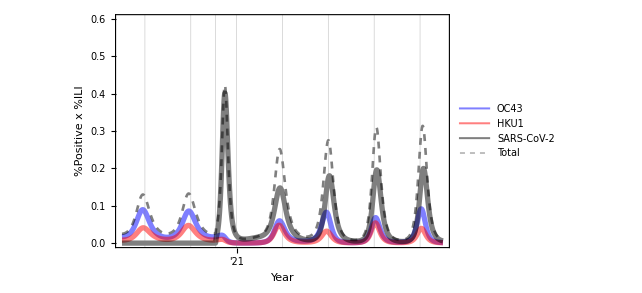

```mathematica
figinvasion
```

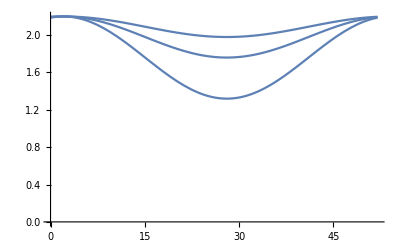

```mathematica
Plot[Table[betaval[t,f,maxR0,phival,1],{f,{0.1, 0.2, 0.4}}],{t, 0, 52}, PlotRange->{0, Automatic}]
```

## Heat maps:

### Examine what happens when we vary cross-immunity:

```mathematica
rundefaults[];
importtime3 = pandemicintro;
parmvecchi = {};
Do[
Do[
chi31val = chi3X;
chi32val = chi3X;
chi13val = chiX3;
chi23val = chiX3;
sol=runmodel3strain[];
totalcuminfnCoV = Evaluate[scalingfactor*cuminfnCoV[plotwindow⟦2⟧]
/.sol]⟦1⟧;
maxpeaknCoV = Max[Flatten[Table[Evaluate[scalingfactor*(S1S2I3[t] + S1E2I3[t] + S1I2I3[t] + S1R2I3[t] + E1S2I3[t] + E1E2I3[t] + E1I2I3[t] + E1R2I3[t] + I1S2I3[t] + I1E2I3[t] + I1I2I3[t] + I1R2I3[t] + R1S2I3[t] + R1E2I3[t] + R1I2I3[t] + R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]]];

parmvecchi = Join[parmvecchi, {{chi3X, chiX3, totalcuminfnCoV, maxpeaknCoV}}]

,{chi3X, RangeN[0,1,16]}]
,{chiX3, RangeN[0,1,16]}]
```

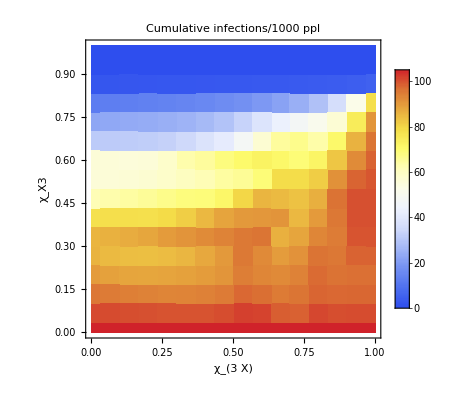

```mathematica
figchicuminf = Show[ListDensityPlot[mult[parmvecchi⟦;;, {1,2,3}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Cumulative infections/1000 ppl", Frame->True, FrameLabel->{"χ_(3  X)", "χ_X3"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->All(*{{0,1},{0,1}}*)]
```

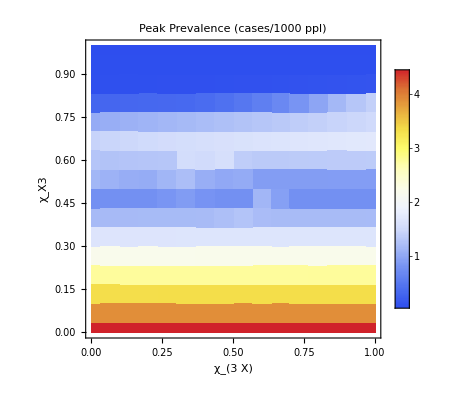

```mathematica
figchimaxpeak = Show[ListDensityPlot[mult[parmvecchi⟦;;, {1,2,4}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Peak Prevalence (cases/1000 ppl)", Frame->True, FrameLabel->{"χ_(3  X)", "χ_X3"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->{{0,1},{0,1}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmap_chicuminflog.pdf", figchicuminf];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmatp_chimaxpeaklog.pdf", figchimaxpeak];
```

### Examine what happens when we vary R0 seasonality and baseline (reset defaults!)

```mathematica
rundefaults[];
importtime3 = pandemicintro;
parmvecR0 = {};
Do[
Do[

maxR0nCoV = R0;
fnCoV = seasonality;

(*sol = runmodel[];*)
sol=runmodel3strain[];
totalcuminfnCoV = Evaluate[scalingfactor*cuminfnCoV[plotwindow⟦2⟧]
/.sol]⟦1⟧;
maxpeaknCoV = Max[Flatten[Table[Evaluate[scalingfactor*(S1S2I3[t] + S1E2I3[t] + S1I2I3[t] + S1R2I3[t] + E1S2I3[t] + E1E2I3[t] + E1I2I3[t] + E1R2I3[t] + I1S2I3[t] + I1E2I3[t] + I1I2I3[t] + I1R2I3[t] + R1S2I3[t] + R1E2I3[t] + R1I2I3[t] + R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]]];

parmvecR0 = Join[parmvecR0, {{R0, seasonality, totalcuminfnCoV, maxpeaknCoV}}]

,{R0, RangeN[2, 2.6, 16]}]
,{seasonality, RangeN[0.1, 0.4,16]}]
```

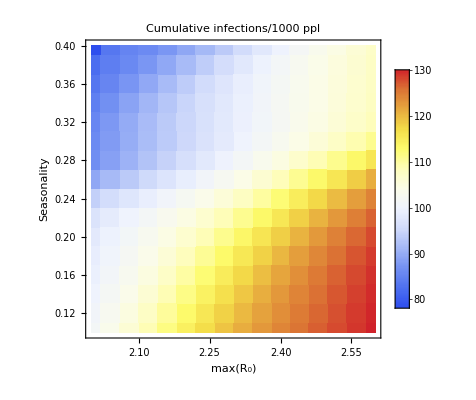

```mathematica
figR0cuminf = Show[ListDensityPlot[mult[parmvecR0⟦;;, {1,2,3}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Cumulative infections/1000 ppl", Frame->True, FrameLabel->{"max(R_0)", "Seasonality"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->All]
```

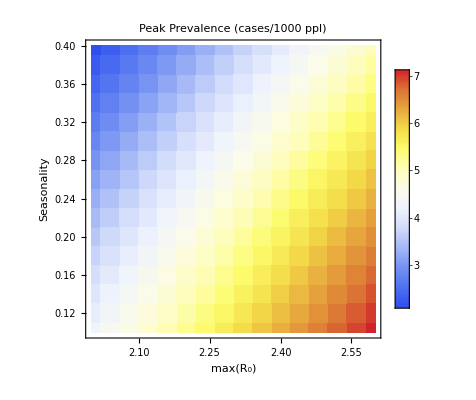

```mathematica
figR0maxpeak =Show[ListDensityPlot[mult[parmvecR0⟦;;, {1,2,4}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Peak Prevalence (cases/1000 ppl)", Frame->True, FrameLabel->{"max(R_0)", "Seasonality"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->All]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmap_R0cuminflog.pdf", figR0cuminf];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmap_R0maxpeaklog.pdf", figR0maxpeak];
```

### Examine what happens when we vary nu and gamma

```mathematica
rundefaults[];
importtime3 = pandemicintro;
parmvecsigimp = {};
Do[
Do[

nuvalnCoV = ν;
gammavalnCoV = γ;

sol = runmodel3strain[];
totalcuminfnCoV = Evaluate[scalingfactor*cuminfnCoV[plotwindow⟦2⟧]
/.sol]⟦1⟧;maxpeaknCoV = Max[Flatten[Table[Evaluate[scalingfactor*(S1S2I3[t] + S1E2I3[t] + S1I2I3[t] + S1R2I3[t] + E1S2I3[t] + E1E2I3[t] + E1I2I3[t] + E1R2I3[t] + I1S2I3[t] + I1E2I3[t] + I1I2I3[t] + I1R2I3[t] + R1S2I3[t] + R1E2I3[t] + R1I2I3[t] + R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]]];

parmvecsigimp = Join[parmvecsigimp, {{ν, γ, totalcuminfnCoV, maxpeaknCoV}}]

,{ν, RangeN[7/10, 7/3, 16]}]
,{γ, RangeN[7/10, 7/3,16]}]
```

```mathematica
parmvecsigimp;
```

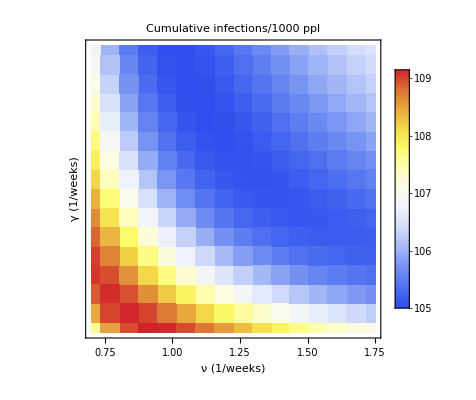

```mathematica
figsigimpcuminf = Show[ListDensityPlot[mult[parmvecsigimp⟦;;, {1,2,3}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Cumulative infections/1000 ppl", Frame->True, FrameLabel->{"ν (1/weeks)", "γ (1/weeks)"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0, FrameTicks->{{{
{52*22+0, "Jan\n2020"},
{52*22+(31+28+31)/7, "Apr\n2020"}, 
{52*22+(31+28+31+30+31+30)/7, "July\n2020"}, 
{52*22+(31+28+31+30+31+30+31+31+30)/7, "Oct\n2020"},
{52*22+52, "Jan\n2021"}},None },{ Automatic, None}}], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->All]
```

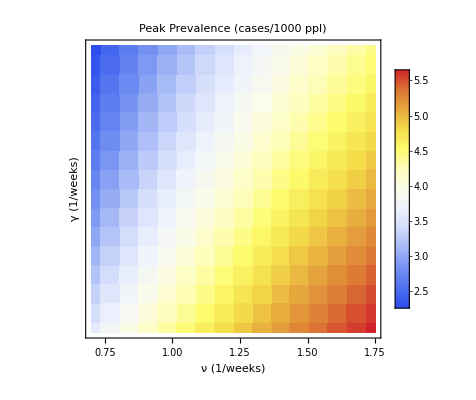

```mathematica
figsigimpmaxpeak =Show[ListDensityPlot[mult[parmvecsigimp⟦;;, {1,2,4}⟧,1000], ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Peak Prevalence (cases/1000 ppl)", Frame->True, FrameLabel->{"ν (1/weeks)", "γ (1/weeks)"}, LabelStyle->Directive[FontSize->14], InterpolationOrder->0, FrameTicks->{{{
{52*22+0, "Jan\n2020"},
{52*22+(31+28+31)/7, "Apr\n2020"}, 
{52*22+(31+28+31+30+31+30)/7, "July\n2020"}, 
{52*22+(31+28+31+30+31+30+31+31+30)/7, "Oct\n2020"},
{52*22+52, "Jan\n2021"}},None },{ Automatic, None}}], 
(*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) 
BaseStyle->FontSize->14, PlotRange->All]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmap_nugamcuminflog.pdf", fignugamcuminf];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/heatmap_nugammaxpeaklog.pdf", fignugammaxpeak];
```

# Single-strain model with exponential waiting times

Plot one-time and intermittent interventions.

## Set parameter values and define functions:

```mathematica
pC = (0.3)*(0.044); (*Probability of needing critical care*)
pH = (0.7)*(0.044); (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)

nuval = 1/(4.6(*4.9*)/7); (*Rate of progressing to infectiousness*)
gammaval = 1/(5/7); (*Rate of losing infectiousness or going to the hospital*)

deltaHval = 1/(8/7); (*Rate of leaving hospital for those not going to critical care*)
deltaCval = 1/(6/7); (*Rate of leaving hospital and going to critical care*)
xiCval = 1/(10/7); (*Rate of leaving critical care*)

maxR0 = 2.2;
f = 0.2;
fullseasonalityfactor = 0.4; 
phival = 2;

kappaval = 0.01;
importtime = (31+29+11)/7; 
importlength = 0.5;

ptest = 0.05; (*probability that a non-hospitalized case gets tested*)

tmax = 5*52;

plotwindow = {0, 64};
plotwindowlong = {0, 52*2.5};
fs = 18;
imsz=400;
seasonality = 1;

thresholdprevon = 0.0035; (*0.00375;*)
thresholdprevoff = 0.0005; (*0.001;*)

thresholdprevonmoreICU = 0.007; (*0.0075*)
thresholdprevoffmoreICU = 0.001; (*0.00025*)
```

## One-time intervention model

```mathematica
runmodeloneshot[] := NDSolve[{
Sq'[t] == -npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Breakpump model

```mathematica
runmodelbreakpump[]:=NDSolve[{
Sq'[t] == -npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon&&npi[t]==1, {npi[t]->1-npifactor, timeson=Join[timeson,{t}]}],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff&&npi[t]<1, {npi[t]->1, timesoff=Join[timesoff,{t}]}],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Breakpump model, more ICU

```mathematica
runmodelbreakpumpmoreICU[]:=NDSolve[{
Sq'[t] == -npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU&&npi[t]==1, {npi[t]->1-npifactor, timeson=Join[timeson,{t}]}],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU&&npi[t]<1, {npi[t]->1, timesoff=Join[timesoff,{t}]}],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios without seasonality:

### No reduction in transmission:

```mathematica
npifactor = 0.0;
npistart = Infinity;
npiend = Infinity;
f=0;
solns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
f=0;
sol20x2x4ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
f=0;
sol40x2x4ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
f=0;
sol60x2x4ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
f=0;
sol20x2x8ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
f=0;
sol40x2x8ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
f=0;
sol60x2x8ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
f=0;
sol20x2x12ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
f=0;
sol40x2x12ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
f=0;
sol60x2x12ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
f=0;
sol20x2x20ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
f=0;
sol40x2x20ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
f=0;
sol60x2x20ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=0;
sol20x2xinfns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=0;
sol40x2xinfns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=0;
sol60x2xinfns=runmodeloneshot[];
```

## Scenarios with seasonality:

### No reduction in transmission:

```mathematica
npifactor = 0.0;
npistart = Infinity;
npiend = Infinity;
f=fullseasonalityfactor;
sols=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
f=fullseasonalityfactor;
sol20x2x4s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
f=fullseasonalityfactor;
sol40x2x4s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
f=fullseasonalityfactor;
sol60x2x4s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
f=fullseasonalityfactor;
sol20x2x8s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
f=fullseasonalityfactor;
sol40x2x8s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
f=fullseasonalityfactor;
sol60x2x8s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
f=fullseasonalityfactor;
sol20x2x12s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
f=fullseasonalityfactor;
sol40x2x12s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
f=fullseasonalityfactor;
sol60x2x12s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
f=fullseasonalityfactor;
sol20x2x20s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
f=fullseasonalityfactor;
sol40x2x20s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
f=fullseasonalityfactor;
sol60x2x20s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=fullseasonalityfactor;
sol20x2xinfs=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=fullseasonalityfactor;
sol40x2xinfs=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
f=fullseasonalityfactor;
sol60x2xinfs=runmodeloneshot[];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
f=0;
timeson = {};
timesoff = {};
sol60bpnsprev=runmodelbreakpump[];
```

```mathematica
timesonnsexp = timeson;
timesoffnsexp = timesoff;
```

## Scenarios with seasonality, with brake-pumping, prevalence-based threshold

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
f=fullseasonalityfactor;
sol60bpsprev=runmodelbreakpump[];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold, and a higher threshold assuming more ICU beds:

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
f=0;
sol60bpnsprevmoreICU=runmodelbreakpumpmoreICU[];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold, and a higher threshold assuming more ICU beds:

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
f=fullseasonalityfactor;
sol60bpsprevmoreICU=runmodelbreakpumpmoreICU[];
```

## Plot incidence without seasonality for one-time interventions (Figure 4):

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 1000;(*1400;*)
```

### Four weeks:

```mathematica
sf = 40;
```

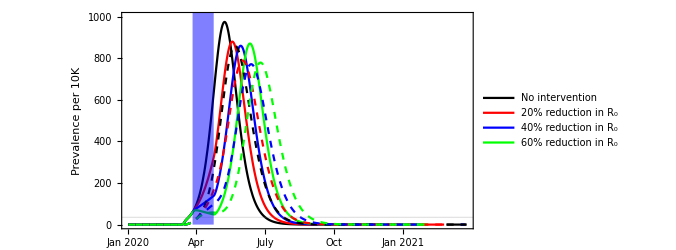

```mathematica
figoneshot4nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4A.pdf",figoneshot4nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4A.png",figoneshot4nscrit];
```

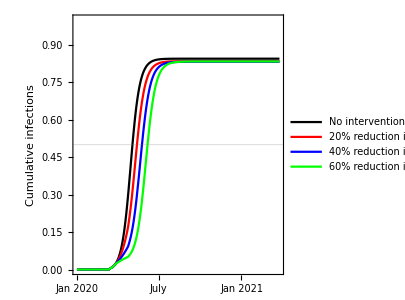

```mathematica
figoneshot4nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x4ns],
Evaluate[1-Sq[t]/.sol40x2x4ns],
Evaluate[1-Sq[t]/.sol60x2x4ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4F.pdf",figoneshot4nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4F.png",figoneshot4nscritcumS];
```

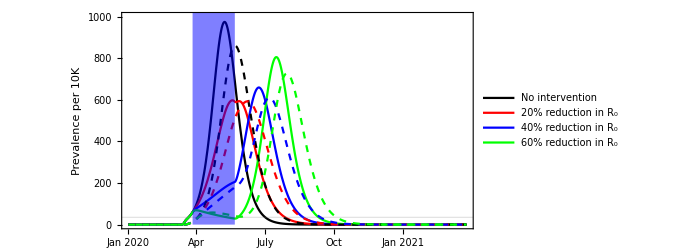

```mathematica
figoneshot8nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4B.pdf",figoneshot8nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4B.png",figoneshot8nscrit];
```

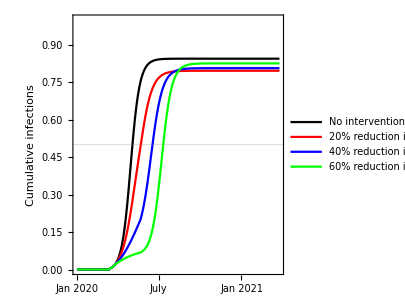

```mathematica
figoneshot8nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x8ns],
Evaluate[1-Sq[t]/.sol40x2x8ns],
Evaluate[1-Sq[t]/.sol60x2x8ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4G.pdf",figoneshot8nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4G.png",figoneshot8nscritcumS];
```

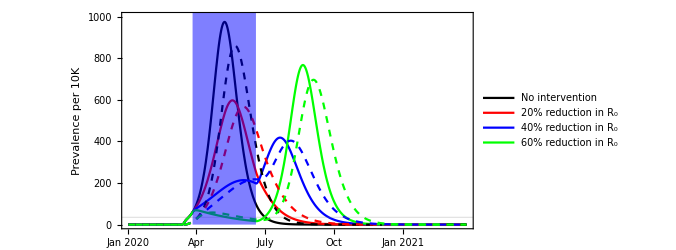

```mathematica
figoneshot12nscrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4C.pdf",figoneshot12nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4C.png",figoneshot12nscrit];
```

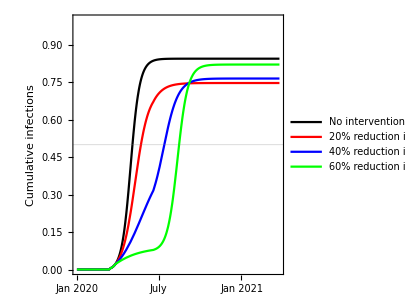

```mathematica
figoneshot12nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x12ns],
Evaluate[1-Sq[t]/.sol40x2x12ns],
Evaluate[1-Sq[t]/.sol60x2x12ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4H.pdf",figoneshot12nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4H.png",figoneshot12nscritcumS];
```

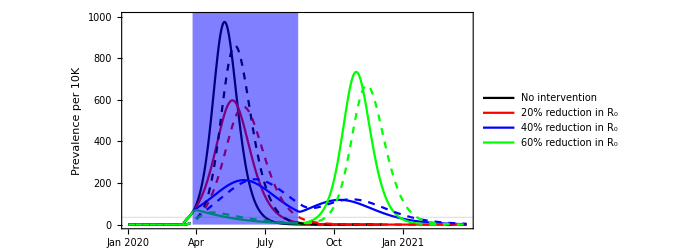

```mathematica
figoneshot20nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4D.pdf",figoneshot20nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4D.png",figoneshot20nscrit];
```

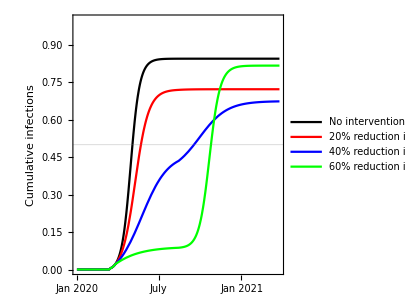

```mathematica
figoneshot20nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x20ns],
Evaluate[1-Sq[t]/.sol40x2x20ns],
Evaluate[1-Sq[t]/.sol60x2x20ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4I.pdf",figoneshot20nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4I.png",figoneshot20nscritcumS];
```

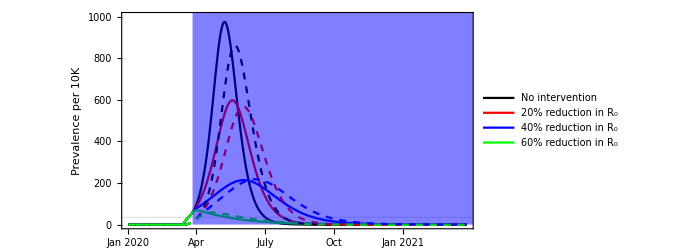

```mathematica
figoneshotinfnscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4E.pdf",figoneshotinfnscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4E.png",figoneshotinfnscrit];
```

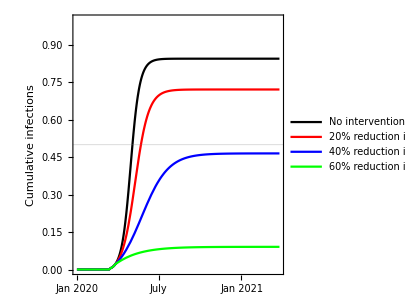

```mathematica
figoneshotinfnscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2xinfns],
Evaluate[1-Sq[t]/.sol40x2xinfns],
Evaluate[1-Sq[t]/.sol60x2xinfns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4J.pdf",figoneshotinfnscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4J.png",figoneshotinfnscritcumS];
```

## Plot incidence with seasonality for one-time interventions (Figure 5):

### Plot characteristics:

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 1000; (*800*)
```

### Four weeks:

```mathematica
sf = 40;
```

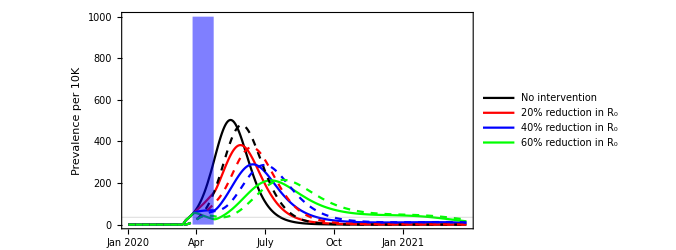

```mathematica
figoneshot4scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5A.pdf",figoneshot4scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5A.png",figoneshot4scrit];
```

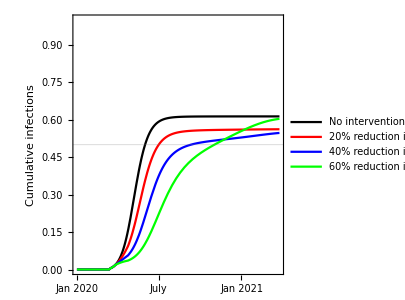

```mathematica
figoneshot4scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x4s],
Evaluate[1-Sq[t]/.sol40x2x4s],
Evaluate[1-Sq[t]/.sol60x2x4s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5F.pdf",figoneshot4scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5F.png",figoneshot4scritcumS];
```

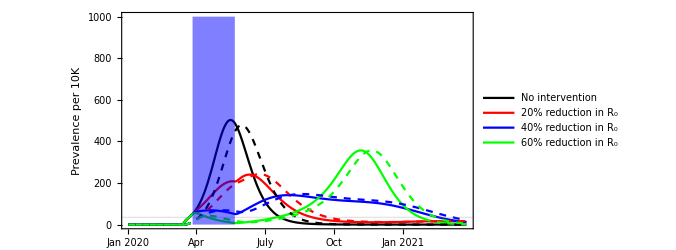

```mathematica
figoneshot8scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5B.pdf",figoneshot8scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5B.png",figoneshot8scrit];
```

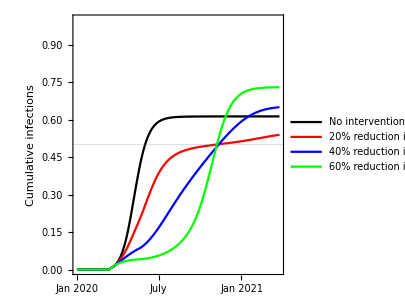

```mathematica
figoneshot8scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x8s],
Evaluate[1-Sq[t]/.sol40x2x8s],
Evaluate[1-Sq[t]/.sol60x2x8s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5G.pdf",figoneshot8scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5G.png",figoneshot8scritcumS];
```

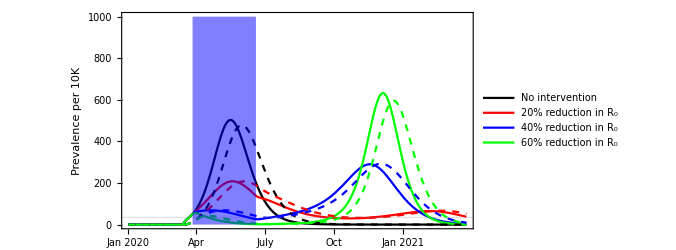

```mathematica
figoneshot12scrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5C.pdf",figoneshot12scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5C.png",figoneshot12scrit];
```

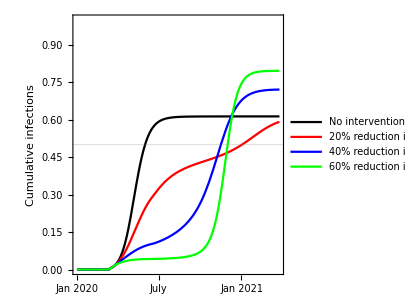

```mathematica
figoneshot12scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x12s],
Evaluate[1-Sq[t]/.sol40x2x12s],
Evaluate[1-Sq[t]/.sol60x2x12s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5H.pdf",figoneshot12scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5H.png",figoneshot12scritcumS];
```

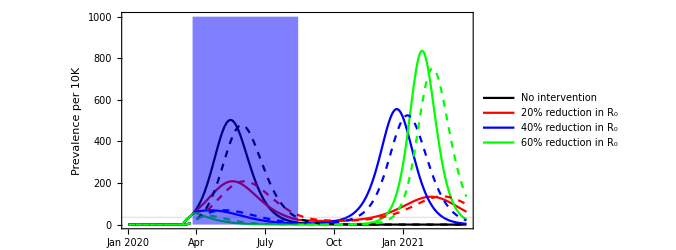

```mathematica
figoneshot20scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5D.pdf",figoneshot20scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5D.png",figoneshot20scrit];
```

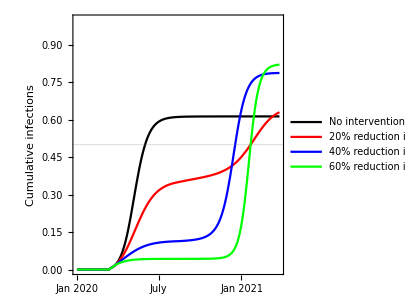

```mathematica
figoneshot20scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x20s],
Evaluate[1-Sq[t]/.sol40x2x20s],
Evaluate[1-Sq[t]/.sol60x2x20s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5I.pdf",figoneshot20scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5I.png",figoneshot20scritcumS];
```

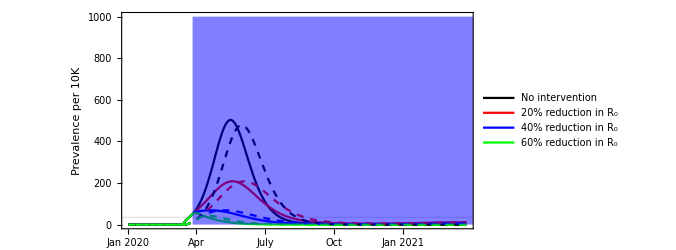

```mathematica
figoneshotinfscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfs], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfs]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5E.pdf",figoneshotinfscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5E.png",figoneshotinfscrit];
```

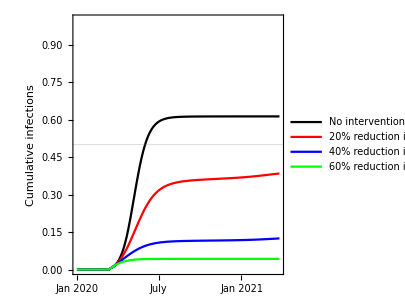

```mathematica
figoneshotinfscritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2xinfs],
Evaluate[1-Sq[t]/.sol40x2xinfs],
Evaluate[1-Sq[t]/.sol60x2xinfs],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5J.pdf",figoneshotinfscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5J.png",figoneshotinfscritcumS];
```

## Define key variables for the brakepump strategies:

```mathematica
dateticks = {
{0, Rotate["Jan",π/2]},
{0, Text[Style["\n\n2020", FontSize->14]]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, Rotate["Apr",π/2]}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["Jan",π/2]},
{52, Text[Style["\n\n2021", FontSize->14]]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["Jan",π/2]}, 
{52*2, Text[Style["\n\n2022", FontSize->14]]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]}};
```

```mathematica
yearticks = {
{0, Rotate["2020",π/2]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, ""}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7,""}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, ""},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["2021",π/2]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7,""}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7,""}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, ""},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["2022",π/2]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7,""}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, ""}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, ""}};
```

```mathematica
ar = 0.25;
```

```mathematica
imsz=700;
```

## Plot breakpump strategy, no seasonality:

```mathematica
sf = 0.02;
prmax = 1.4;
```

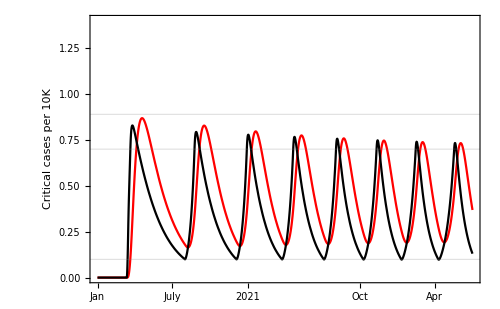

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, prmax}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

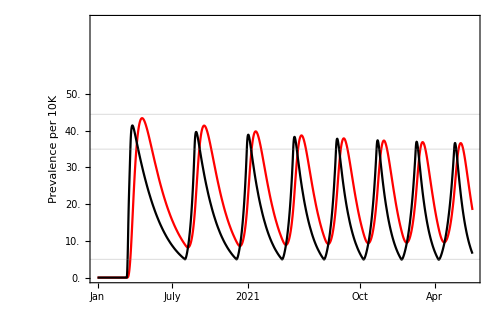

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, prmax}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0,1},5],All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibp = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

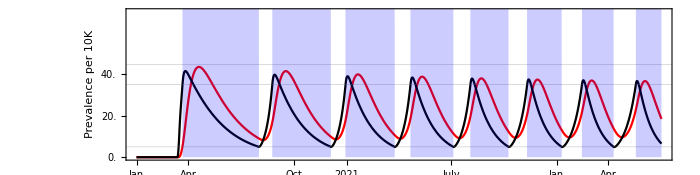

```mathematica
figcritprevbpnpi = Show[{figcritprevbp, fignpibp}, PlotRange->PlotRange[figcritprevbp], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6A.pdf",figcritprevbpnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6A.png",figcritprevbpnpi];
```

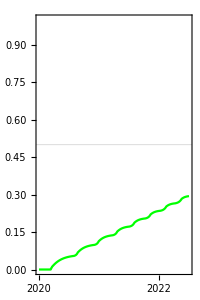

```mathematica
figcritprevbpnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"},PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}, ImageSize-> 200]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6E.pdf",figcritprevbpnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6E.png",figcritprevbpnpiimm];
```

## Plot breakpump strategy, with seasonality:

```mathematica
sf = 0.02;
prmax = 1;
```

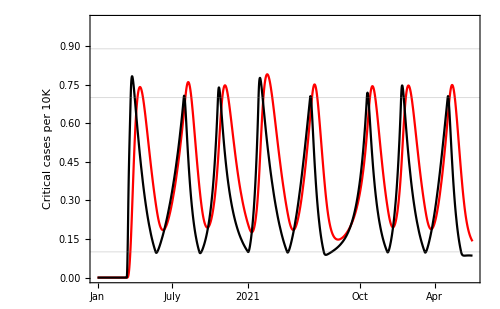

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

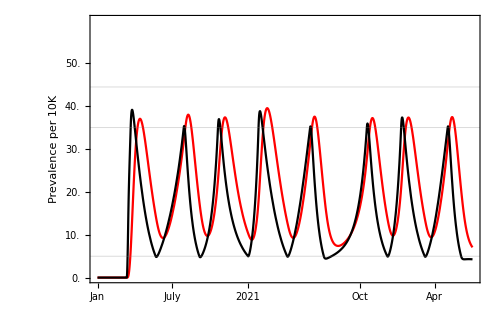

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

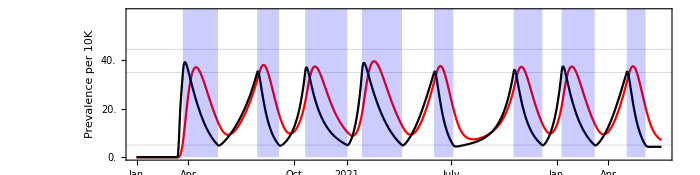

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6B.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6B.png",figcritprevbpsnpi];
```

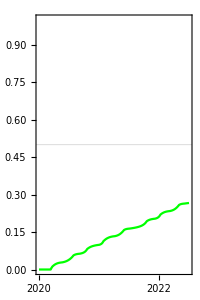

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6F.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6F.png",figcritprevbpsnpiimm];
```

## Plot breakpump strategy, no seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
prmax = 2;
```

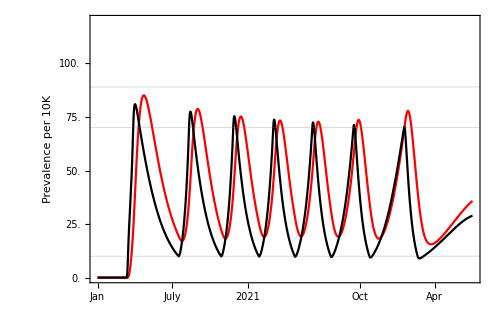

```mathematica
figcritprevbpnsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpnsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprevmoreICU],{t,0,500}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

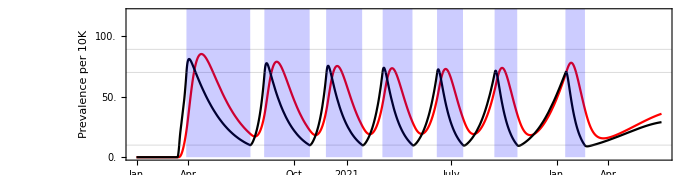

```mathematica
figcritprevbpnsnpimoreICU = Show[{figcritprevbpnsmoreICU, fignpibpnsmoreICU}, PlotRange->PlotRange[figcritprevbpnsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6C.pdf",figcritprevbpnsnpimoreICU];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6C.png",figcritprevbpnsnpimoreICU];
```

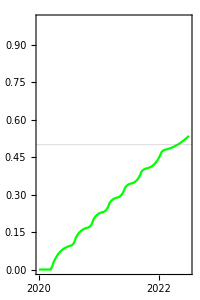

```mathematica
figcritprevbpnsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{ },{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6G.pdf",figcritprevbpnsnpimoreICUimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6G.png",figcritprevbpnsnpimoreICUimm];
```

## Plot breakpump strategy, with seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
prmax = 2;
```

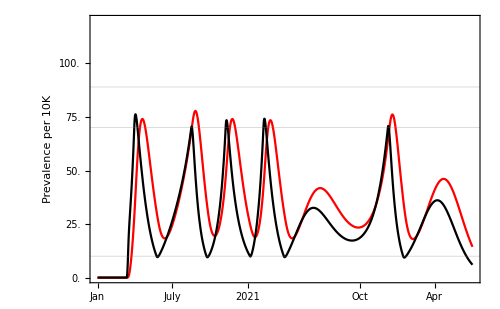

```mathematica
figcritprevbpsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpsprevmoreICU],{t,0,500}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

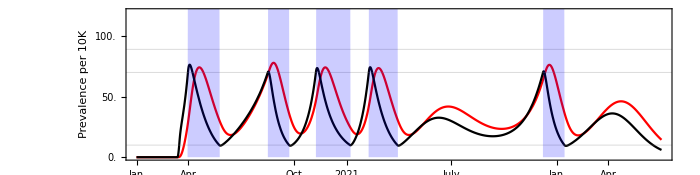

```mathematica
figcritprevbpsnpimoreICU = Show[{figcritprevbpsmoreICU, fignpibpsmoreICU}, PlotRange->PlotRange[figcritprevbpsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6D.pdf",figcritprevbpsnpimoreICU];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6D.png",figcritprevbpsnpimoreICU];
```

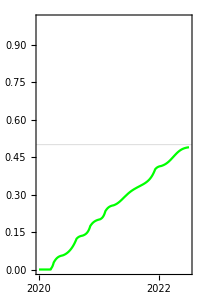

```mathematica
figcritprevbpsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6H.pdf",figcritprevbpsnpimoreICUimm];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6H.png",figcritprevbpsnpimoreICUimm];
```

## Plot some heat maps to explore different thresholds:

```mathematica
tmax = 2.5*52;
```

```mathematica
CCthreshold = 0.000089;
```

```mathematica
npiduration[timeson_, timesoff_] := If[Length[timesoff]<Length[timeson], Total[Join[timesoff, {tmax}]- timeson], Total[timesoff-timeson]];
```

```mathematica
npifactor = 0.6;
f=0;(* fullseasonalityfactor;*)
```

```mathematica
thresholdprevonrng = Range[0.0001,0.004, 0.0001];
thresholdprevoffrng = Range[0.0001, 0.004, 0.0001];
```

```mathematica
output = {};
Do[
(*Print[tpon];*)
Do[

thresholdprevon = tpon;
thresholdprevoff = tpoff;
If[thresholdprevoff ≥ thresholdprevon, Continue[]];

timeson={};
timesoff={};
sol=runmodelbreakpump[];

maxCC = Max[Flatten[Table[Evaluate[CCq[t]/.sol],{t,0,tmax,0.01}]]];
If[maxCC>CCthreshold, Continue[]];

output = Join[output, {{thresholdprevon, thresholdprevoff, npiduration[timeson, timesoff]/tmax, Length[timeson], maxCC}}];

,{tpoff, thresholdprevoffrng}]
,{tpon, thresholdprevonrng}]
```

Find the ‘optimal’ set of thresholds:

```mathematica
Position[(output⟦;;,3⟧*output⟦;;,4⟧),Min[(output⟦;;,3⟧*output⟦;;,4⟧)]]
```

{{137}}

```mathematica
output⟦567⟧;
```

Part::partw: Part 567 of {{0.0002,0.0001,0.882423,5,0.0000763516},{0.0003,0.0001,0.878543,4,0.0000766556},{0.0003,0.0002,0.874933,8,0.0000766556},{0.0004,0.0001,0.868782,4,0.0000770255},«44»,{0.0011,0.0004,0.839955,6,0.0000810678},{0.0011,0.0005,0.839214,8,0.0000810678},«103»} does not exist.

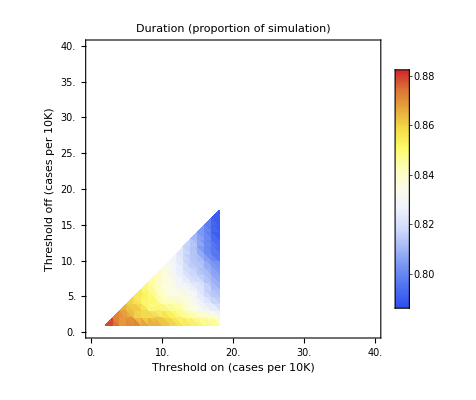

```mathematica
figduration = Show[ListDensityPlot[output⟦;;, {1,2,3}⟧, ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Duration (proportion of simulation)", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]], (*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
Export["~/Desktop/durationR26nslog.png", figduration];
```

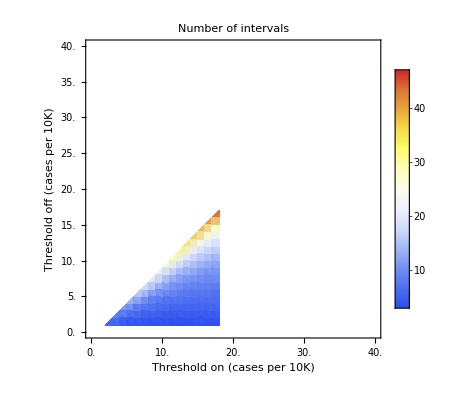

```mathematica
figintervals = Show[ListDensityPlot[output⟦;;, {1,2,4}⟧,ColorFunction->"TemperatureMap" ,PlotLegends->Automatic, PlotLabel->"Number of intervals", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]](*,ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}]*), BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
Export["~/Desktop/intervalsR26nslog.png", figintervals];
```

## Plot some heat maps to explore different thresholds with doubled ICU capacity (not used in paper):

```mathematica
CCthreshold = 0.000089;
```

```mathematica
npiduration[timeson_, timesoff_] := If[Length[timesoff]<Length[timeson], Total[Join[timesoff, {tmax}]- timeson], Total[timesoff-timeson]];
```

```mathematica
npifactor = 0.6;
f=0; (*fullseasonalityfactor*)
```

```mathematica
thresholdprevonrng = Range[0.0001, 0.008, 0.0001];
thresholdprevoffrng = Range[0.0001,0.008, 0.0001];
```

```mathematica
output = {};
Do[
Print[tpon];
Do[

thresholdprevon = tpon;
thresholdprevoff= tpoff;
If[thresholdprevoff ≥ thresholdprevon, Continue[]];

timeson={};
timesoff={};
sol=runmodelbreakpump[];

maxCC = Max[Flatten[Table[Evaluate[CCq[t]/.sol],{t,0,tmax,0.01}]]];
If[maxCC>2*CCthreshold, Continue[]];

output = Join[output, {{thresholdprevon, thresholdprevoff, npiduration[timeson, timesoff]/tmax, Length[timeson], maxCC}}];

,{tpoff, thresholdprevoffrng}]
,{tpon, thresholdprevonrng}]
```

0.0001

0.0002

0.0003

0.0004

0.0005

0.0006

0.0007

0.0008

0.0009

0.001

0.0011

0.0012

0.0013

0.0014

0.0015

0.0016

0.0017

0.0018

0.0019

0.002

0.0021

0.0022

0.0023

0.0024

0.0025

0.0026

0.0027

0.0028

0.0029

0.003

0.0031

0.0032

0.0033

0.0034

0.0035

0.0036

0.0037

0.0038

0.0039

0.004

0.0041

0.0042

0.0043

0.0044

0.0045

0.0046

0.0047

0.0048

0.0049

0.005

0.0051

0.0052

0.0053

0.0054

0.0055

0.0056

0.0057

0.0058

0.0059

0.006

0.0061

0.0062

0.0063

0.0064

0.0065

0.0066

0.0067

0.0068

0.0069

0.007

0.0071

0.0072

0.0073

0.0074

0.0075

0.0076

0.0077

0.0078

0.0079

0.008

Find the ‘optimal’ set of thresholds:

```mathematica
Position[(output⟦;;,3⟧*output⟦;;,4⟧),Min[(output⟦;;,3⟧*output⟦;;,4⟧)]]
```

{{2467}}

```mathematica
output⟦567⟧;
```

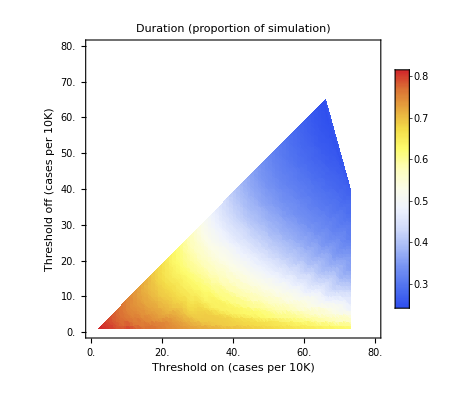

```mathematica
figduration = Show[ListDensityPlot[output⟦;;, {1,2,3}⟧, ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Duration (proportion of simulation)", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]], (*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) BaseStyle->FontSize->14, PlotRange->{{0,80/10000},{0,80/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
(*Export["~/Desktop/durationR22nslog_moreicu.png", figduration];*)
```

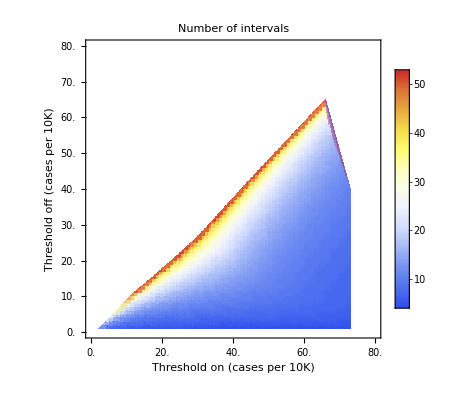

```mathematica
figintervals = Show[ListDensityPlot[output⟦;;, {1,2,4}⟧,ColorFunction->"TemperatureMap" ,PlotLegends->Automatic, PlotLabel->"Number of intervals", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]](*,ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}]*), BaseStyle->FontSize->14, PlotRange->{{0,80/10000},{0,80/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
(*Export["~/Desktop/intervalsR22nslog_moreicu.png", figintervals];*)
```

# Single-strain model with multiple compartments

Generate a multi-compartment model to have Gamma-distributed waiting times

## Define new thresholds:

```mathematica
thresholdprevon = 0.0025; (*0.00375;*)
thresholdprevoff = 0.0005; (*0.001;*)

thresholdprevonmoreICU = 0.005; (*0.0075*)
thresholdprevoffmoreICU = 0.001; (*0.00025*)
```

## Define the model:

```mathematica
nrep = 5;
runmodelGaussian[] := NDSolve[{
Sq'[t] == -npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t])*Sq[t] - est[t]*Sq[t],

Eq1'[t] == npi[t]*betaval[t, f, maxR0, phival, gammaval]*(ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t])*Sq[t] + est[t]*Sq[t] - nrep*nuval*Eq1[t],
Eq2'[t] == nrep*nuval*Eq1[t] - nrep*nuval*Eq2[t] ,
Eq3'[t] == nrep*nuval*Eq2[t] - nrep*nuval*Eq3[t] ,
Eq4'[t] == nrep*nuval*Eq3[t] - nrep*nuval*Eq4[t] ,
Eq5'[t] == nrep*nuval*Eq4[t] - nrep*nuval*Eq5[t] ,

ISq1'[t] == nrep*pS*nuval*Eq5[t] - nrep*gammaval*ISq1[t],
ISq2'[t] == nrep*gammaval*ISq1[t] - nrep*gammaval*ISq2[t],
ISq3'[t] == nrep*gammaval*ISq2[t] - nrep*gammaval*ISq3[t],
ISq4'[t] == nrep*gammaval*ISq3[t] - nrep*gammaval*ISq4[t],
ISq5'[t] == nrep*gammaval*ISq4[t] - nrep*gammaval*ISq5[t],
RSq'[t] == nrep*gammaval*ISq5[t],

IHq1'[t] == nrep*pH*nuval*Eq5[t] - nrep*gammaval*IHq1[t],
IHq2'[t] == nrep*gammaval*IHq1[t] - nrep*gammaval*IHq2[t],
IHq3'[t] == nrep*gammaval*IHq2[t] - nrep*gammaval*IHq3[t],
IHq4'[t] == nrep*gammaval*IHq3[t] - nrep*gammaval*IHq4[t],
IHq5'[t] == nrep*gammaval*IHq4[t] - nrep*gammaval*IHq5[t],

HHq1'[t]== nrep*gammaval*IHq5[t] - nrep*deltaHval*HHq1[t], 
HHq2'[t] ==  nrep*deltaHval*HHq1[t] -  nrep*deltaHval*HHq2[t],
HHq3'[t] ==  nrep*deltaHval*HHq2[t] -  nrep*deltaHval*HHq3[t],
HHq4'[t] ==  nrep*deltaHval*HHq3[t] -  nrep*deltaHval*HHq4[t],HHq5'[t] ==  nrep*deltaHval*HHq4[t] -  nrep*deltaHval*HHq5[t],

RHq'[t] == nrep*deltaHval*HHq5[t],

ICq1'[t] == nrep*pC*nuval*Eq5[t] - nrep*gammaval*ICq1[t],
ICq2'[t] == nrep*gammaval*ICq1[t] - nrep*gammaval*ICq2[t],
ICq3'[t] == nrep*gammaval*ICq2[t] - nrep*gammaval*ICq3[t],
ICq4'[t] == nrep*gammaval*ICq3[t] - nrep*gammaval*ICq4[t],
ICq5'[t] == nrep*gammaval*ICq4[t] - nrep*gammaval*ICq5[t],

HCq1'[t] == nrep*gammaval*ICq5[t] - nrep*deltaCval*HCq1[t],
HCq2'[t] == nrep*deltaCval*HCq1[t] -nrep*deltaCval*HCq2[t] , 
HCq3'[t] == nrep*deltaCval*HCq2[t] -nrep*deltaCval*HCq3[t] , 
HCq4'[t] == nrep*deltaCval*HCq3[t] -nrep*deltaCval*HCq4[t] , HCq5'[t] == nrep*deltaCval*HCq4[t] -nrep*deltaCval*HCq5[t] , 

CCq1'[t] ==nrep*deltaCval*HCq5[t] - nrep*xiCval*CCq1[t],
CCq2'[t] ==nrep*xiCval*CCq1[t] - nrep*xiCval*CCq2[t],
CCq3'[t] ==nrep*xiCval*CCq2[t] - nrep*xiCval*CCq3[t],
CCq4'[t] ==nrep*xiCval*CCq3[t] - nrep*xiCval*CCq4[t],CCq5'[t] ==nrep*xiCval*CCq4[t] - nrep*xiCval*CCq5[t],

RCq'[t] == nrep*xiCval*CCq5[t],

est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]>thresholdprevon&&npi[t]==1, {npi[t]->1-npifactor, timeson=Join[timeson,{t}]}],
WhenEvent[ISq1[t] + ISq2[t] + ISq3[t] + ISq4[t] + ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]<thresholdprevoff&&npi[t]<1, {npi[t]->1, timesoff=Join[timesoff,{t}]}],
Sq[0]==1,
Eq1[0]==0,Eq2[0]==0,Eq3[0]==0,Eq4[0]==0,Eq5[0]==0,
ISq1[0]==0,ISq2[0]==0,ISq3[0]==0,ISq4[0]==0,ISq5[0]==0,
RSq[0]==0,
IHq1[0]==0,IHq2[0]==0,IHq3[0]==0,IHq4[0]==0,IHq5[0]==0,
HHq1[0]==0,HHq2[0]==0,HHq3[0]==0,HHq4[0]==0,HHq5[0]==0,
RHq[0]==0,
ICq1[0]==0,ICq2[0]==0,ICq3[0]==0,ICq4[0]==0,ICq5[0]==0,
HCq1[0]==0,HCq2[0]==0,HCq3[0]==0,HCq4[0]==0,HCq5[0]==0,
CCq1[0]==0,CCq2[0]==0,CCq3[0]==0,CCq4[0]==0,CCq5[0]==0,
RCq[0]==0,
est[0]==0, npi[0]==1
},{Sq, 
Eq1, Eq2, Eq3, Eq4, Eq5, 
ISq1,ISq2,ISq3,ISq4,ISq5, 
RSq, 
IHq1, IHq2, IHq3, IHq4, IHq5, 
HHq1, HHq2, HHq3, HHq4, HHq5, 
RHq, 
ICq1, ICq2, ICq3, ICq4, ICq5, 
HCq1, HCq2, HCq3, HCq4, HCq5, 
CCq1, CCq2, CCq3, CCq4, CCq5, 
RCq, 
est, npi},{t, 0, tmax}
];
```

## Run the model:

### With seasonality:

```mathematica
npifactor = 0.6;
f=fullseasonalityfactor;
sol60bpsprevGaussian  = runmodelGaussian[];
```

### Without seasonality:

```mathematica
timeson = {};
timesoff = {};
npifactor = 0.6;
f=0;
sol60bpnsprevGaussian  = runmodelGaussian[];
```

```mathematica
timesonnsgam = timeson;
timesoffnsgam = timesoff;
```

```mathematica
Mean[Drop[timesonnsexp,1] - Drop[timesoffnsexp,-1]]
```

5.15223

```mathematica
Mean[Drop[timesonnsgam,1] - Drop[timesoffnsgam,-1]]
```

4.99544

```mathematica
timesonnsexp
```

{11.0086,31.5494,48.1819,63.0966,76.8591,89.8033,102.149,114.054,125.641,137.01,148.25,159.446,170.684,182.063,193.697,205.742,218.418,232.089,247.447}

```mathematica
Mean[timesoffnsexp - timesonnsexp]
```

7.78276

```mathematica
Mean[timesoffnsgam - timesonnsgam]
```

6.16319

### With more ICU beds and seasonality:

```mathematica
oldthresholdprevon = thresholdprevon;
oldthresholdprevoff = thresholdprevoff;
thresholdprevon = thresholdprevonmoreICU;
thresholdprevoff = thresholdprevoffmoreICU;
npifactor = 0.6;
f=fullseasonalityfactor;
sol60bpsprevmoreICUGaussian  = runmodelGaussian[];
thresholdprevon = oldthresholdprevon ;
thresholdprevoff = oldthresholdprevoff;
```

### With more ICU beds, no seasonality:

```mathematica
oldthresholdprevon = thresholdprevon;
oldthresholdprevoff = thresholdprevoff;
thresholdprevon = thresholdprevonmoreICU;
thresholdprevoff = thresholdprevoffmoreICU;
npifactor = 0.6;
f=0;
sol60bpnsprevmoreICUGaussian  = runmodelGaussian[];
thresholdprevon = oldthresholdprevon ;
thresholdprevoff = oldthresholdprevoff;
```

## Plot breakpump strategy, with seasonality:

```mathematica
sf = 0.02;
prmax = 1;
```

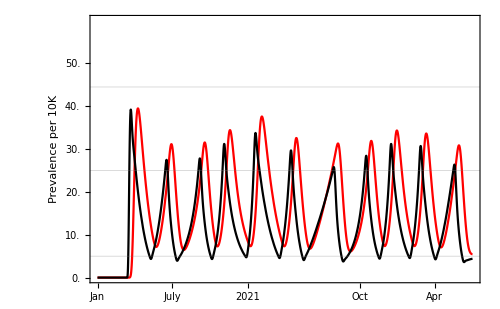

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol60bpsprevGaussian],
10000*sf*Evaluate[ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]/.sol60bpsprevGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpsprevGaussian],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

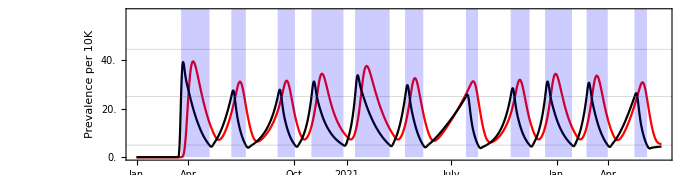

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Bmulticomp.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Bmulticomp.png",figcritprevbpsnpi];
```

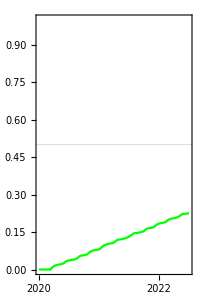

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprevGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Fmulticomp.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Fmulticomp.png",figcritprevbpsnpiimm];
```

## Plot breakpump strategy, no seasonality:

```mathematica
sf = 0.02;
prmax = 1;
```

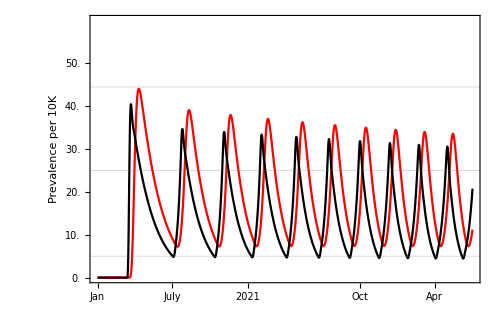

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol60bpnsprevGaussian],
10000*sf*Evaluate[ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]/.sol60bpnsprevGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprevGaussian],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

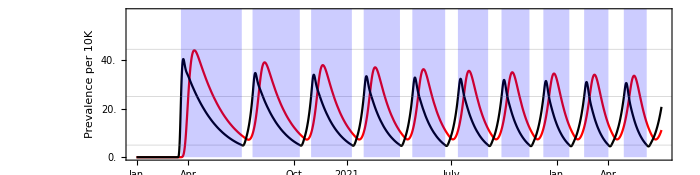

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Amulticomp.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Amulticomp.png",figcritprevbpsnpi];
```

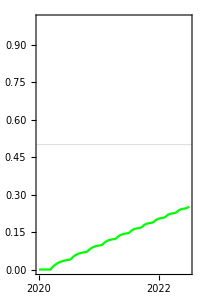

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprevGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Emulticomp.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Emulticomp.png",figcritprevbpsnpiimm];
```

## Plot breakpump strategy, with seasonality and higher ICU capacity:

```mathematica
sf = 0.02;
prmax = 2;
```

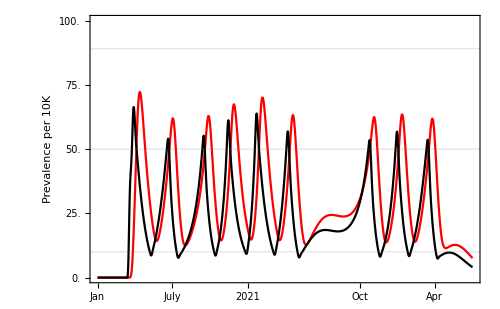

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol60bpsprevmoreICUGaussian],
10000*sf*Evaluate[ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]/.sol60bpsprevmoreICUGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, prmax}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}}, {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpsprevmoreICUGaussian],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

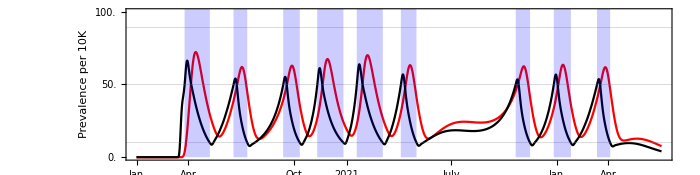

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Dmulticomp.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Dmulticomp.png",figcritprevbpsnpi];
```

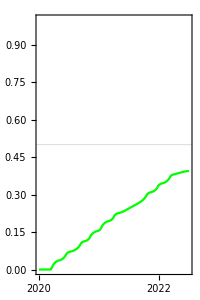

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprevmoreICUGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Hmulticomp.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Hmulticomp.png",figcritprevbpsnpiimm];
```

## Plot breakpump strategy, no seasonality with higher ICU capacity:

```mathematica
sf = 0.02;
prmax = 2.2;
```

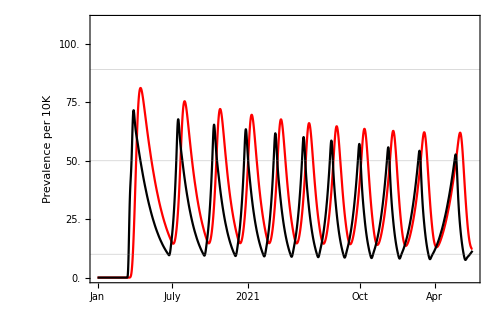

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol60bpnsprevmoreICUGaussian],
10000*sf*Evaluate[ISq1[t] +ISq2[t] +ISq3[t] +ISq4[t] +ISq5[t] + 
IHq1[t] + IHq2[t] + IHq3[t] + IHq4[t] + IHq5[t] + 
ICq1[t]+ICq2[t]+ICq3[t]+ICq4[t]+ICq5[t]/.sol60bpnsprevmoreICUGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, prmax}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}}, {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprevmoreICUGaussian],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

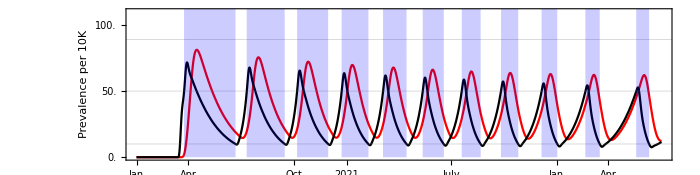

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Cmulticomp.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Cmulticomp.png",figcritprevbpsnpi];
```

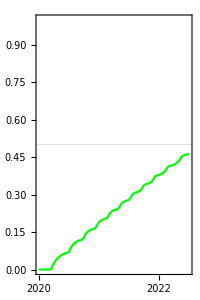

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprevmoreICUGaussian]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Gmulticomp.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6Gmulticomp.png",figcritprevbpsnpiimm];
```

## Plot the waiting time distributions:

```mathematica
Mean[GammaDistribution[1, 7/nuval]]
```

4.6

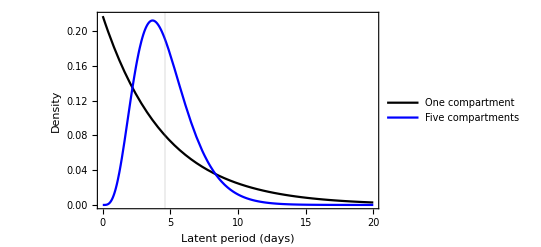

```mathematica
fignudist = Plot[{
PDF[GammaDistribution[1, 7/nuval],x],
PDF[GammaDistribution[5, 7/nuval/5],x]
},{x,0,20}, GridLines->{{{7/nuval, {Black, Dashed, Opacity[1]}}},{}}, PlotRange->All, Frame->{True,True,False,False}, PlotLegends->{"One compartment", "Five compartments"}, PlotStyle->{Black, Blue}, FrameLabel->{"Latent period (days)","Density"}, BaseStyle->FontSize->14]
```

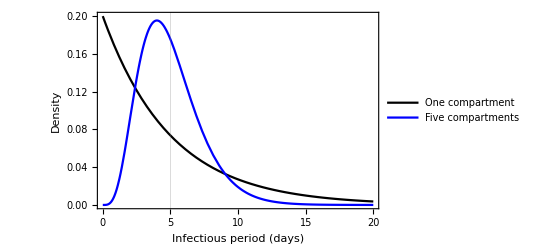

```mathematica
figgammadist = Plot[{
PDF[GammaDistribution[1, 7/gammaval],x],
PDF[GammaDistribution[5, 7/gammaval/5],x]
},{x,0,20}, GridLines->{{{7/gammaval, {Black, Dashed, Opacity[1]}}},{}}, PlotRange->All, Frame->{True,True,False,False},PlotLegends->{"One compartment", "Five compartments"}, PlotStyle->{Black, Blue}, FrameLabel->{"Infectious period (days)","Density"}, BaseStyle->FontSize->14]
```

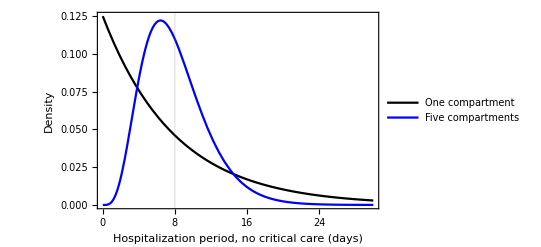

```mathematica
figdeltaHdist = Plot[{
PDF[GammaDistribution[1, 7/deltaHval],x],
PDF[GammaDistribution[5, 7/deltaHval/5],x]
},{x,0,30}, GridLines->{{{7/deltaHval,{Black, Dashed, Opacity[1]}}},{}}, PlotRange->All, Frame->{True,True,False,False},PlotLegends->{"One compartment", "Five compartments"}, PlotStyle->{Black, Blue}, FrameLabel->{"Hospitalization period, no critical care (days)","Density"}, BaseStyle->FontSize->14]
```

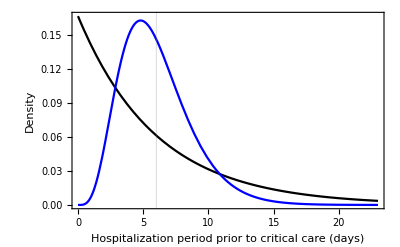

```mathematica
figdeltaCdist = Plot[{
PDF[GammaDistribution[1, 7/deltaCval],x],
PDF[GammaDistribution[5, 7/deltaCval/5],x]
},{x,0,23}, GridLines->{{{7/deltaCval,{Black, Dashed, Opacity[1]}}},{}}, PlotRange->All, Frame->{True,True,False,False}, PlotStyle->{Black, Blue}, FrameLabel->{"Hospitalization period prior to critical care (days)","Density"}, BaseStyle->FontSize->14]
```

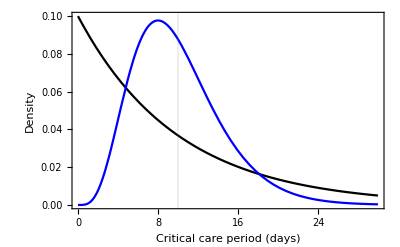

```mathematica
figxiCdist = Plot[{
PDF[GammaDistribution[1, 7/xiCval],x],
PDF[GammaDistribution[5, 7/xiCval/5],x]
},{x,0,30}, GridLines->{{{7/xiCval,{Black, Dashed, Opacity[1]}}},{}}, PlotRange->All, Frame->{True,True,False,False}, PlotStyle->{Black, Blue}, FrameLabel->{"Critical care period (days)","Density"}, BaseStyle->FontSize->14]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/nudist.png", fignudist];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/gammadist.png", figgammadist];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/deltaHdist.png", figdeltaHdist];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/deltaCdist.png", figdeltaCdist];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/figures/xiCdist.png", figxiCdist];
```

## Plot some heat maps to explore different thresholds:

```mathematica
tmax = 2.5*52;
```

```mathematica
CCthreshold = 0.000089;
```

```mathematica
npiduration[timeson_, timesoff_] := If[Length[timesoff]<Length[timeson], Total[Join[timesoff, {tmax}]- timeson], Total[timesoff-timeson]];
```

```mathematica
npifactor = 0.6;
f=0; (*fullseasonalityfactor*)
```

```mathematica
thresholdprevonrng = Range[0.0001,0.004, 0.0001];
thresholdprevoffrng = Range[0.0001, 0.004, 0.0001];
```

```mathematica
output = {};
Do[
Print[tpon];
Do[

thresholdprevon = tpon;
thresholdprevoff = tpoff;
If[thresholdprevoff ≥ thresholdprevon, Continue[]];

timeson={};
timesoff={};
sol=runmodelGaussian[];

maxCC = Max[Flatten[Table[Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol],{t,0,tmax,0.01}]]];
If[maxCC>CCthreshold, Continue[]];

output = Join[output, {{thresholdprevon, thresholdprevoff, npiduration[timeson, timesoff]/tmax, Length[timeson], maxCC}}];

,{tpoff, thresholdprevoffrng}]
,{tpon, thresholdprevonrng}]
```

0.0001

0.0002

0.0003

0.0004

0.0005

0.0006

0.0007

0.0008

0.0009

0.001

0.0011

0.0012

0.0013

0.0014

0.0015

0.0016

0.0017

0.0018

0.0019

0.002

0.0021

0.0022

0.0023

0.0024

0.0025

Find the ‘optimal’ set of thresholds:

```mathematica
Position[(output⟦;;,3⟧*output⟦;;,4⟧),Min[(output⟦;;,3⟧*output⟦;;,4⟧)]]
```

{{277}}

```mathematica
output⟦567⟧;
```

Part::partw: Part 567 of {} does not exist.

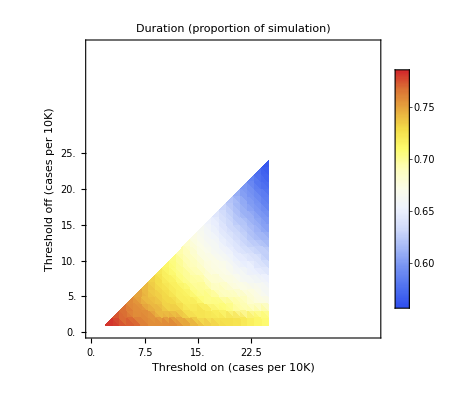

```mathematica
figduration = Show[ListDensityPlot[output⟦;;, {1,2,3}⟧, ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Duration (proportion of simulation)", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]], (*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
Export["~/Desktop/durationhighRns_new.png", figduration];
```

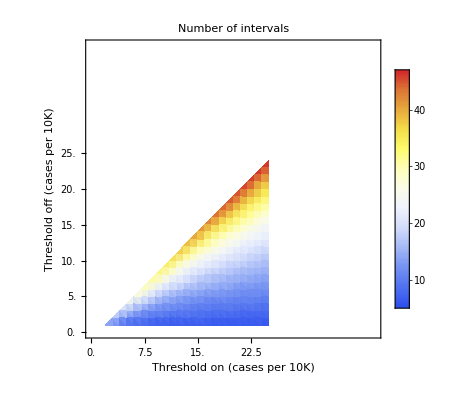

```mathematica
figintervals = Show[ListDensityPlot[output⟦;;, {1,2,4}⟧,ColorFunction->"TemperatureMap" ,PlotLegends->Automatic, PlotLabel->"Number of intervals", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]](*,ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}]*), BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
Export["~/Desktop/intervalshighRns_new.png", figintervals];
```

## Plot some heat maps to explore different thresholds with doubled ICU capacity:

```mathematica
CCthreshold = 0.000089;
```

```mathematica
npiduration[timeson_, timesoff_] := If[Length[timesoff]<Length[timeson], Total[Join[timesoff, {tmax}]- timeson], Total[timesoff-timeson]];
```

```mathematica
npifactor = 0.6;
f=0; (*fullseasonalityfactor*)
```

```mathematica
thresholdprevonrng = Range[0.0001, 0.008, 0.0001];
thresholdprevoffrng = Range[0.0001,0.008, 0.0001];
```

```mathematica
output = {};
Do[
Print[tpon];
Do[

thresholdprevon = tpon;
thresholdprevoff= tpoff;
If[thresholdprevoff ≥ thresholdprevon, Continue[]];

timeson={};
timesoff={};
sol=runmodelGaussian[];

maxCC = Max[Flatten[Table[Evaluate[CCq1[t]+CCq2[t]+CCq3[t]+CCq4[t]+CCq5[t]/.sol],{t,0,tmax,0.01}]]];
If[maxCC>2*CCthreshold, Continue[]];

output = Join[output, {{thresholdprevon, thresholdprevoff, npiduration[timeson, timesoff]/tmax, Length[timeson], maxCC}}];

,{tpoff, thresholdprevoffrng}]
,{tpon, thresholdprevonrng}]
```

$Aborted

Find the ‘optimal’ set of thresholds:

```mathematica
Position[(output⟦;;,3⟧*output⟦;;,4⟧),Min[(output⟦;;,3⟧*output⟦;;,4⟧)]]
```

{{277}}

```mathematica
output⟦567⟧;
```

Part::partw: Part 567 of {{0.0002,0.0001,0.872728,6,0.0000640259},{0.0003,0.0001,0.878505,4,0.0000643209},{0.0003,0.0002,0.868248,9,0.0000643209},«45»,{0.0011,0.0004,0.835174,7,0.0000686127},{0.0011,0.0005,0.826419,9,0.0000686127},«250»} does not exist.

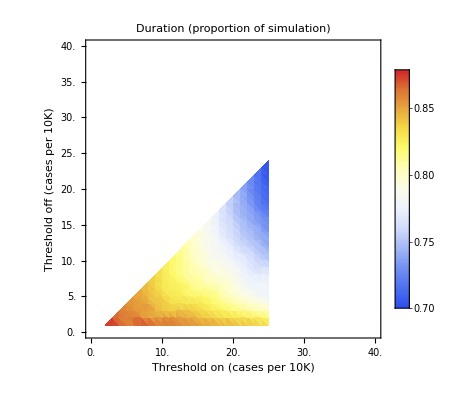

```mathematica
figduration = Show[ListDensityPlot[output⟦;;, {1,2,3}⟧, ColorFunction->"TemperatureMap", PlotLegends->Automatic, PlotLabel->"Duration (proportion of simulation)", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]], (*ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}],*) BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
(*Export["~/Desktop/durationhighRns_new.png", figduration];*)
```

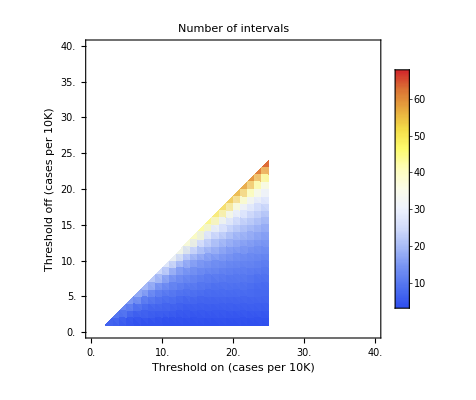

```mathematica
figintervals = Show[ListDensityPlot[output⟦;;, {1,2,4}⟧,ColorFunction->"TemperatureMap" ,PlotLegends->Automatic, PlotLabel->"Number of intervals", Frame->True, FrameLabel->{"Threshold on (cases per 10K)", "Threshold off (cases per 10K)"}, LabelStyle->Directive[FontSize->14]](*,ListPlot[{{0.0025,0.0001}}, PlotStyle->{Black, PointSize[Large]}]*), BaseStyle->FontSize->14, PlotRange->{{0,40/10000},{0,40/10000}},FrameTicks->{{#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevonrng],Max[thresholdprevonrng]}, 10]], {#, ToString[#*10000]}&/@N[FindDivisions[{Min[thresholdprevoffrng],Max[thresholdprevoffrng]}, 10]], None, None}]
```

```mathematica
(*Export["~/Desktop/intervalshighRns_new.png", figintervals];*)
```